# Five-point near-planar Landshoff region and central-soft MRK

Outcome. For the topology below, generic non-coplanar five-particle wide-angle kinematics has no positive Landau pinch. A hidden region appears instead in the exactly massless, near-planar limit Gamma5=epsilon5^2 -> 0. Its invariant description, factorized cancellation ideal, lower-facet certificate and power counting are established in Part I. Part II then uses one exact set of dimensionless variables to compare this angular approach to planarity with the central-soft MRK approach. Both limits have a certified HR, but their cancellation ideals, physical region vectors, momentum modes and scalar powers are different. No off-shell regulator and no MRK hierarchy are used in Part I.

## 1. Reproducible setup and graph

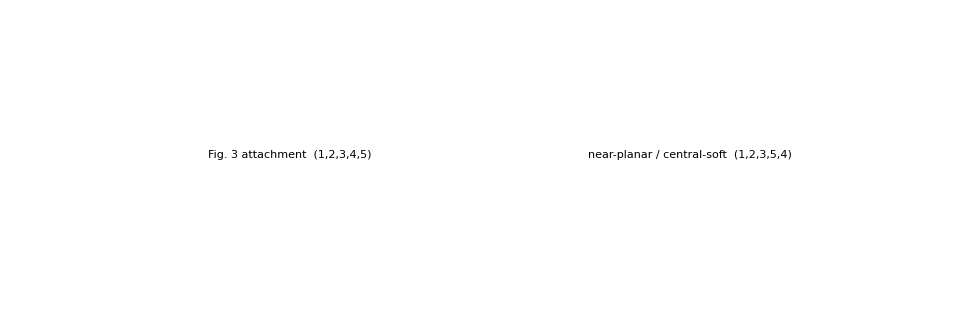

```mathematica
$HRF5WALandshoffAuditLibraryOnly=True;Get[FileNameJoin[{NotebookDirectory[],"HRF_FivePointWideAngleLandshoffAllLayerAudit.wl"}]];landshoffAudit=hrf5WALandshoffAllLayerAudit[];
```

Both panels keep exactly the internal vertex positions and topology of Fig. 3. Incoming p2 and p1 enter from the upper- and lower-left, while p3,p4,p5 end at the upper, middle and lower right. The left panel is the canonical spacelike-collinear attachment. The near-planar and representative central-soft calculation instead interchanges the external attachments p4 and p5 without moving the internal vertices; consequently their two external lines cross in this physical layout. The crossing is not a vertex.

use | external labels at vertices (1,2,3,4,5)
spacelike-collinear / Fig. 3 | (1,2,3,4,5)
near-planar and representative central-soft | (1,2,3,5,4)

The earlier paper figure is one-based, whereas the executable notebooks are zero-based. The following map is used everywhere below:

internal edge | Fig. 3 / paper label | code / this notebook
(1,3) | x1 | x0
(1,5) | x2 | x1
(2,3) | x3 | x2
(2,5) | x4 | x3
(3,4) | x5 | x4
(4,5) | x6 | x5

Abstractly, the internal graph is a theta graph: three equivalent two-edge paths connect the four-valent vertices carrying p3 and, in the second panel, p4. Its path-permutation symmetry remains exact.

path | edge pair | middle external leg | ratio
A | (x0,x1) | p1 | rA=x0/x1
B | (x2,x3) | p2 | rB=x2/x3
C | (x4,x5) | p5 | rC=x4/x5

The common endpoints carry p3 and p4. The middle vertices of paths A,B,C carry p1,p2,p5, respectively. All internal propagators are massless, so U and F are multilinear in every original edge variable.

## Part I. Invariant Mandelstam analysis

## 2. Exactly massless five-point kinematics

All momenta are written in the all-outgoing convention, with p1 and p2 incoming physically. Throughout Part I, p_i^2=0 exactly. Five adjacent Mandelstam invariants may be used as coordinates; all remain of the same wide-angle order. The full physical sign domain is:

class | invariants | sign
incoming-incoming | s12 | >0
outgoing-outgoing | s34, s45, s35 | >0
incoming-outgoing | s23, s15, s13, s14, s24, s25 | <0
non-coplanar interior | Gamma5=epsilon5^2 | Gamma5<0
chosen orientation | epsilon5/i | >0

{s13==-s12-s23+s45,s14==-s15+s23-s45,s24==s15-s23-s34,s25==-s12-s15+s34,s35==s12-s34-s45}

To avoid a convention clash with the parity-odd square root, denote the real Gram determinant by Gamma5:

Gamma5==s12^2 s15^2-2 s12^2 s15 s23+s12^2 s23^2-2 s12 s15^2 s45+2 s12 s15 s23 s34+2 s12 s15 s23 s45+2 s12 s15 s34 s45-2 s12 s23^2 s34+2 s12 s23 s34 s45+s15^2 s45^2+2 s15 s23 s34 s45-2 s15 s34 s45^2+s23^2 s34^2-2 s23 s34^2 s45+s34^2 s45^2==epsilon5^2

epsilon5==4 ⅈ LeviCivita(p1,p2,p3,p4)

For real physical momenta epsilon5 is purely imaginary. Our orientation is epsilon5/i=+Sqrt[-Gamma5], so Gamma5<0 in the non-coplanar interior. The Landau surface is the coplanar boundary Gamma5=0, approached physically as Gamma5->0 from below and epsilon5/i->0 from above. This statement is entirely invariant.

(0 | s12 | -s12-s23+s45 | -s15+s23-s45
s12 | 0 | s23 | s15-s23-s34
-s12-s23+s45 | s23 | 0 | s34
-s15+s23-s45 | s15-s23-s34 | s34 | 0)

s12^2 s15^2-2 s12^2 s15 s23+s12^2 s23^2-2 s12 s15^2 s45+2 s12 s15 s23 s34+2 s12 s15 s23 s45+2 s12 s15 s34 s45-2 s12 s23^2 s34+2 s12 s23 s34 s45+s15^2 s45^2+2 s15 s23 s34 s45-2 s15 s34 s45^2+s23^2 s34^2-2 s23 s34^2 s45+s34^2 s45^2==0

In this notebook F denotes the complete massless on-shell second Symanzik polynomial. For the chosen near-planar expansion, F0=F|_(Gamma5=0) is the leading polynomial and the normal correction begins at Gamma5=O(lambda^2). No external off-shell regulator is introduced.

### 2.1 Manifestly symmetric graph polynomials

U==(x0+x1) (x2+x3)+(x0+x1) (x4+x5)+(x2+x3) (x4+x5)

Introduce one dimensionless ratio on each path:

{rA==x0/x1,rB==x2/x3,rC==x4/x5}

Φ(rA,rB,rC)==ellA rA+ellB rB+ellC rC+qAB rA rB+qBC rB rC+qCA rA rC

F==x1 x3 x5 Φ(rA,rB,rC)

The function Φ is only a convenient dimensionless ratio polynomial obtained by factoring x1 x3 x5 out of F. It is not another graph polynomial.

All kinematic dependence is contained in six coefficients expressed only through adjacent invariants:

coefficient | invariants
qAB | s12-s34-s45
qBC | -s12-s23+s45
qCA | s23
ellA | -s15+s23-s45
ellB | s15-s23-s34
ellC | s45

Only their ratios matter. If a dimensionless parametrization is preferred, divide all six coefficients and all s_ij by the common scale s12; none of the stationary equations or generator statements changes.

The form of U and Φ is covariant under permutations of A,B,C. Relabelling the corresponding external legs simply permutes the q and ell coefficients.

### Expanded on-shell F, if required

s12 x0 x2 x5-s12 x1 x2 x4-s15 x0 x3 x5+s15 x1 x2 x5+s23 x0 x3 x4+s23 x0 x3 x5-s23 x1 x2 x4-s23 x1 x2 x5-s34 x0 x2 x5-s34 x1 x2 x5-s45 x0 x2 x5-s45 x0 x3 x5+s45 x1 x2 x4+s45 x1 x3 x4

## 3. Positive Landau locus in invariant variables

The variables x1,x3,x5 are convenient positive coordinates for the common magnitude on each two-edge path: x0=rA x1, x2=rB x3 and x4=rC x5. They are not fixed overall constants; together with the ratios they form six independent coordinates on the positive Schwinger orthant. Since F=x1 x3 x5 Φ(r), the ratio part of the Landau equations is grad_r Φ=0. Explicit differentiation gives grad_r Φ=K.r+ell: for example, dΦ/drA=qAB rB+qCA rC+ellA. Therefore at the stationary ratio r=rho one obtains K.rho=-ell.

K==(0 | qAB | qCA
qAB | 0 | qBC
qCA | qBC | 0)

K.{rhoA,rhoB,rhoC}=={-ellA,-ellB,-ellC}

This linear system determines rho uniquely whenever qAB qBC qCA is nonzero. There is no advantage in displaying the lengthy components of K^(-1) ell individually.

At this generic kinematic point, before imposing any coplanar or MRK limit, define the three normal polynomials

{fA==x0-rhoA x1,fB==x2-rhoB x3,fC==x4-rhoC x5}

Φ(rhoA,rhoB,rhoC)==Gamma5/(4 qAB qBC qCA)

This is not a second Φ: it is the same function evaluated at its stationary point r=rho. Completing the quadratic form about rho gives an exact identity for the full massless F at generic five-point kinematics:

F==fA fB qAB x5+fA fC qCA x3+fB fC qBC x1+(Gamma5 x1 x3 x5)/(4 qAB qBC qCA)

### Analytic check from the Mandelstam polynomial

The following executable check starts from the usual expanded on-shell Symanzik polynomial in the adjacent Mandelstam invariants, stored under Graph/F0 and displayed in the closed subsection of Sec. 2. It then substitutes the explicit invariant q coefficients, the exact solution rho=-K^(-1).ell, the definitions of fA,fB,fC, and the Gram polynomial. No use is made of the ratio-form identity being tested.

```mathematica
Fmandelstam=Expand[landshoffAudit["Graph","F0"]];qRules=Normal[landshoffAudit["InvariantSymmetricForm","QuadraticCoefficients"]];rhoRules=Thread[{rhoA,rhoB,rhoC}->landshoffAudit["InvariantSymmetricForm","StationaryRatioVector"]];fRules={fA->x0-rhoA x1,fB->x2-rhoB x3,fC->x4-rhoC x5};gammaRule=Gamma5->hrf5WAGramDeterminant[];rhs=qAB x5 fA fB+qBC x1 fB fC+qCA x3 fC fA+(Gamma5 x1 x3 x5)/(4 qAB qBC qCA);Factor[Together[Fmandelstam-(rhs/.fRules/.rhoRules/.qRules/.gammaRule)]]
```

0

The zero is an exact symbolic identity for generic adjacent Mandelstam invariants; no numerical kinematic point or coplanar restriction has been used.

### What the derivative harvester sees

The compact factorized identity must not be confused with the algorithmic input. Starting from the usual Mandelstam polynomial, the raw first derivative is

D_0==ellA x3 x5+qAB x2 x5+qCA x3 x4

Literal collection in qAB, qCA and ellA exposes only monomials. The first component of K.rho=-ell gives ellA=-qAB rhoB-qCA rhoC, and only then can the same derivative be reorganized as

D_0==qAB x5 (x2-rhoB x3)+qCA x3 (x4-rhoC x5)==fB qAB x5+fC qCA x3

Thus the simple appearance of fB and fC has already used the stationary reorganisation. On Gamma5=0 the complete leading polynomial is the selected cancellation sector, so its candidate-specific saturated gradient ideal may derive this consequence of the raw derivatives after localising away from the nonzero determinant, without supplying rho in advance. This would not be a valid pre-decomposition operation on a polynomial that still contained an obstruction.

The Gamma5 remainder is independent of x0,x2,x4. Hence three derivatives of the full F, with no restriction to Gamma5=0, are

{(∂F)/(∂x0)==fB qAB x5+fC qCA x3,(∂F)/(∂x2)==fA qAB x5+fC qBC x1,(∂F)/(∂x4)==fA qCA x3+fB qBC x1}

Their coefficient matrix in (fA,fB,fC) has determinant 2 qAB qBC qCA x1 x3 x5. In the interior positive orthant it therefore forces fA=fB=fC=0. On that locus the remaining derivatives are Gamma5 (x3 x5,x1 x5,x1 x3)/(4 qAB qBC qCA), and F itself is Gamma5 x1 x3 x5/(4 qAB qBC qCA). Thus the full derivative system first exposes the candidate normal ideal and then requires Gamma5=0 for an actual pinch.

First-sheet Schwinger positivity selects rhoA,rhoB,rhoC>0. The orientation sign of epsilon5 does not enter F, but the physical boundary must be reachable from the domain epsilon5/i>0. For example, the following invariant point lies on that boundary and satisfies every two-particle sign condition:

{s12,s23,s34,s45,s15}=={45,-3,9/2,27,-45/2}

{rhoA,rhoB,rhoC}=={4,1,2}

Gamma5==epsilon5==0

### Exact positive Landau check

The stored invariant construction verifies the stationary equations, the Gram identity and positivity without exposing any dimensionful light-cone parametrization.

```mathematica
landshoffAudit["InvariantSymmetricForm"]
```

## 4. Coplanar leading sector and factorized generators

Only now specialise the generic construction to the coplanar boundary. The cancellation structure remains in the original edge variables and is defined before dissection.

### Compact form in the exact dimensionless variables

Define zeta=-1/w and zetabar=-1/wbar. On the coplanar boundary zeta=zetabar=xi>0, with X34=p3+/p4+ and X45=p4+/p5+. The three stationary ratios then have a particularly transparent form:

R==(X45 (xi+1)+xi)/(X34 X45 (xi+1)+1)

{rhoA==R X34 xi,rhoB==R,rhoC==xi}

{fA==x0-R x1 X34 xi,fB==x2-R x3,fC==x4-x5 xi}

For the physical positive-Landau branch X34>0, X45>0 and xi>0. Therefore R>0 and rhoA,rhoB,rhoC are all positive. These expressions are exactly the invariant solution K.rho=-ell rewritten in the common five-point variables; no MRK hierarchy has been taken.

The f_i define the Landau locus but are not HRF generators individually: a generator must have the factorized structure needed by the Landau equations. The three generators are their pairwise products:

generator | factorized form | multiplier in F0
G_AB | fA fB | qAB x5
G_BC | fB fC | qBC x1
G_CA | fA fC | qCA x3

Using kappa for four coordinates tangent to the Gram surface and Gamma5 as a local normal coordinate, the chosen kinematic expansion is

F(Gamma5,kappa)==Gamma5 F_Gamma5(kappa)+F_0(kappa)+remainder(Gamma5^2)

There is no conflict between the nonlinear-looking exact decomposition and the linearity of F in Mandelstam invariants. Gamma5 is itself a nonlinear polynomial in those invariants. Replacing one Mandelstam variable by Gamma5 is a nonlinear change of kinematic coordinates, so F_Gamma5=(dF/dGamma5)_kappa contains the corresponding nonlinear Jacobian. Equivalently, the rational kinematic dependence of rho=-K^(-1).ell cancels between the separate terms of the exact decomposition, restoring the original Mandelstam-linear polynomial.

Away from the stationary locus the complete F_Gamma5 depends on the choice of tangent coordinates kappa. Its restriction to fA=fB=fC=0 is invariantly fixed by the exact decomposition to x1 x3 x5/(4 qAB qBC qCA). This is not an obstruction in the technical HRF sense, because it is absent from F0 by the definition of the expansion rather than being demoted by the HR scaling. Since Gamma5=O(lambda^2), this contribution first appears two powers beyond F0. Its precise weight relative to the cancelled leading sector and to U follows only after the region vector has been determined below.

F_0==fA fB qAB x5+fA fC qCA x3+fB fC qBC x1

### Recovering the path normals from derivatives

The stationary-adapted derivatives displayed in Sec. 3 recover the three normals after the raw derivatives of the selected Gamma5=0 leading sector have been completed inside its saturated gradient ideal. Since qAB=s35, qBC=s13 and qCA=s23, the resulting outer sectors expose the normals directly up to positive monomial factors. For example, the two sectors in the first derivative expose fB and fC. In the Crown this sector form is available directly; here the f_i contain kinematic stationary ratios, so the reorganisation itself must first be derived.

After saturation by the nonzero determinant, the ideal of these three derivatives is <fA,fB,fC>. The remaining derivatives select Gamma5=0. Only there does substitution into F0 reconstruct the HR generator ideal <fA fB,fB fC,fC fA>. Each term contains three distinct edge variables, so the original F remains cubic and multi-affine; no x_e^2 occurs. Quadratic powers of local variables may arise only after changing coordinates.

### End-to-end HRF run in the original variables

The following run implements the same logic without supplying the three normals or their pairwise products. The expansion is first fixed on Gamma5=0; there the complete supplied leading polynomial equals the cancellation sector, and HRF is explicitly authorised to saturate its gradient ideal. Kinematic prefactors that are nonzero in the stated domain are treated as units: polynomial division is in the Schwinger variables, with rational functions of the Mandelstams as coefficients. The Gram equation certifies that the remainder is absent from the leading kinematic surface; its physical order lambda^2 is restored separately in the scaling step. This special use of saturation is not the general derivative-harvest step for a polynomial containing an obstruction.

```mathematica
$HRF5WANearPlanarAlgorithmAuditLibraryOnly=True;Get[FileNameJoin[{NotebookDirectory[],"HRF_FivePointNearPlanarAlgorithmAudit.wl"}]];algorithmResult=hrf5WANearPlanarAlgorithmAudit[];algorithmResult["Summary"]
```

certificate | value
normal factors recovered | 3
candidate generator-set histogram | <|3 -> 1, 2 -> 3, 1 -> 4|>
valid decompositions | 1
generators in surviving set | 3
region vector (v0,...,v5) | {-2, -2, -2, -2, -2, -2}
weights (WSL,WHR) | {-6, -4}
hidden region / truncated | {True, False}

Exactly one decomposition survives: the set of all three pairwise generators. Every candidate containing only one or two of them leaves a nonzero remainder on Gamma5=0. Exact coverage then recovers the primitive physical vector and the gap quoted in Sec. 5. The search is uncapped and untruncated.

### Recovered factors and generators

```mathematica
KeyTake[algorithmResult["Scan"],{"CancellationFactors","Generators","ObstructionData","CoverageScalingData"}]
```

<|CancellationFactors→{2 s12 s15 x4+4 s15 s23 x4-2 s23^2 x4-2 s23 s34 x4-2 s15 s45 x4+2 s23 s45 x4+2 s34 s45 x4-s12 s15 x5-4 s15^2 x5+s12 s23 x5+6 s15 s23 x5-2 s23^2 x5+4 s15 s34 x5-3 s23 s34 x5-3 s15 s45 x5+2 s23 s45 x5+3 s34 s45 x5,s12 s15 x2-s12 s23 x2+s23 s34 x2+2 s12 s45 x2-s15 s45 x2+2 s23 s45 x2-s34 s45 x2-2 s45^2 x2-2 s15 s45 x3+2 s23 s45 x3-2 s45^2 x3,2 s12 s15 x0-2 s15 s45 x0+2 s23 s45 x0+2 s34 s45 x0-s12 s15 x1+s12 s23 x1-s23 s34 x1-3 s15 s45 x1+2 s23 s45 x1+3 s34 s45 x1},Generators→{(2 s12 s15 x0-2 s15 s45 x0+2 s23 s45 x0+2 s34 s45 x0-s12 s15 x1+s12 s23 x1-s23 s34 x1-3 s15 s45 x1+2 s23 s45 x1+3 s34 s45 x1) (s12 s15 x2-s12 s23 x2+s23 s34 x2+2 s12 s45 x2-s15 s45 x2+2 s23 s45 x2-s34 s45 x2-2 s45^2 x2-2 s15 s45 x3+2 s23 s45 x3-2 s45^2 x3),(2 s12 s15 x0-2 s15 s45 x0+2 s23 s45 x0+2 s34 s45 x0-s12 s15 x1+s12 s23 x1-s23 s34 x1-3 s15 s45 x1+2 s23 s45 x1+3 s34 s45 x1) (2 s12 s15 x4+4 s15 s23 x4-2 s23^2 x4-2 s23 s34 x4-2 s15 s45 x4+2 s23 s45 x4+2 s34 s45 x4-s12 s15 x5-4 s15^2 x5+s12 s23 x5+6 s15 s23 x5-2 s23^2 x5+4 s15 s34 x5-3 s23 s34 x5-3 s15 s45 x5+2 s23 s45 x5+3 s34 s45 x5),(s12 s15 x2-s12 s23 x2+s23 s34 x2+2 s12 s45 x2-s15 s45 x2+2 s23 s45 x2-s34 s45 x2-2 s45^2 x2-2 s15 s45 x3+2 s23 s45 x3-2 s45^2 x3) (2 s12 s15 x4+4 s15 s23 x4-2 s23^2 x4-2 s23 s34 x4-2 s15 s45 x4+2 s23 s45 x4+2 s34 s45 x4-s12 s15 x5-4 s15^2 x5+s12 s23 x5+6 s15 s23 x5-2 s23^2 x5+4 s15 s34 x5-3 s23 s34 x5-3 s15 s45 x5+2 s23 s45 x5+3 s34 s45 x5)},ObstructionData→<|Indices→{},ObstructionTerms→{(s12^3 s15^3 s23 x1 x3 x4)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),-((s12^3 s15^2 s23^2 x1 x3 x4)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),(s12^2 s15^3 s23^2 x1 x3 x4)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),(s12^3 s15 s23^3 x1 x3 x4)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),-((5 s12^2 s15^2 s23^3 x1 x3 x4)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),(2 s12^2 s15 s23^4 x1 x3 x4)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),-((s12^2 s23^5 x1 x3 x4)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),(s12^2 s15^2 s23^2 s34 x1 x3 x4)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),(2 s12 s15^2 s23^3 s34 x1 x3 x4)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),-((s12^2 s23^4 s34 x1 x3 x4)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),-((3 s12 s15 s23^4 s34 x1 x3 x4)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),(s12 s23^5 s34 x1 x3 x4)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),-((s12 s15 s23^3 s34^2 x1 x3 x4)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),(s12 s23^4 s34^2 x1 x3 x4)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),(s15 s23^4 s34^2 x1 x3 x4)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),-((s23^5 s34^2 x1 x3 x4)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),-((s23^4 s34^3 x1 x3 x4)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),-((s12^3 s15^3 s45 x1 x3 x4)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),(2 s12^3 s15^2 s23 s45 x1 x3 x4)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),-((7 s12^2 s15^3 s23 s45 x1 x3 x4)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),-((s12^3 s15 s23^2 s45 x1 x3 x4)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),(15 s12^2 s15^2 s23^2 s45 x1 x3 x4)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),-((2 s12 s15^3 s23^2 s45 x1 x3 x4)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),-((11 s12^2 s15 s23^3 s45 x1 x3 x4)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),(3 s12 s15^2 s23^3 s45 x1 x3 x4)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),(3 s12^2 s23^4 s45 x1 x3 x4)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),-((s12 s15 s23^4 s45 x1 x3 x4)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),(s12^2 s15^2 s23 s34 s45 x1 x3 x4)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),-((s12 s15^2 s23^2 s34 s45 x1 x3 x4)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),(3 s12^2 s23^3 s34 s45 x1 x3 x4)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),(8 s12 s15 s23^3 s34 s45 x1 x3 x4)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),(2 s15^2 s23^3 s34 s45 x1 x3 x4)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),-((4 s12 s23^4 s34 s45 x1 x3 x4)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),-((s15 s23^4 s34 s45 x1 x3 x4)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),-((4 s12 s23^3 s34^2 s45 x1 x3 x4)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),-((11 s15 s23^3 s34^2 s45 x1 x3 x4)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),(5 s23^4 s34^2 s45 x1 x3 x4)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),(5 s23^3 s34^3 s45 x1 x3 x4)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),(3 s12^2 s15^3 s45^2 x1 x3 x4)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),-((5 s12^2 s15^2 s23 s45^2 x1 x3 x4)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),(11 s12 s15^3 s23 s45^2 x1 x3 x4)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),(3 s12^2 s15 s23^2 s45^2 x1 x3 x4)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),-((8 s12 s15^2 s23^2 s45^2 x1 x3 x4)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),(s15^3 s23^2 s45^2 x1 x3 x4)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),-((s12^2 s23^3 s45^2 x1 x3 x4)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),(3 s12 s15 s23^3 s45^2 x1 x3 x4)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),-((s15^2 s23^3 s45^2 x1 x3 x4)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),-((3 s12^2 s15^2 s34 s45^2 x1 x3 x4)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),-((9 s12 s15^2 s23 s34 s45^2 x1 x3 x4)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),-((s12^2 s23^2 s34 s45^2 x1 x3 x4)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),-((3 s12 s15 s23^2 s34 s45^2 x1 x3 x4)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),-((15 s15^2 s23^2 s34 s45^2 x1 x3 x4)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),(5 s12 s23^3 s34 s45^2 x1 x3 x4)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),(4 s15 s23^3 s34 s45^2 x1 x3 x4)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),(7 s12 s15 s23 s34^2 s45^2 x1 x3 x4)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),(5 s12 s23^2 s34^2 s45^2 x1 x3 x4)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),(11 s15 s23^2 s34^2 s45^2 x1 x3 x4)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),-((9 s23^3 s34^2 s45^2 x1 x3 x4)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),-((9 s23^2 s34^3 s45^2 x1 x3 x4)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),-((3 s12 s15^3 s45^3 x1 x3 x4)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),(4 s12 s15^2 s23 s45^3 x1 x3 x4)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),-((5 s15^3 s23 s45^3 x1 x3 x4)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),-((2 s12 s15 s23^2 s45^3 x1 x3 x4)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),(3 s15^2 s23^2 s45^3 x1 x3 x4)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),(6 s12 s15^2 s34 s45^3 x1 x3 x4)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),-((2 s12 s15 s23 s34 s45^3 x1 x3 x4)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),(17 s15^2 s23 s34 s45^3 x1 x3 x4)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),-((2 s12 s23^2 s34 s45^3 x1 x3 x4)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),-((5 s15 s23^2 s34 s45^3 x1 x3 x4)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),-((3 s12 s15 s34^2 s45^3 x1 x3 x4)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),-((2 s12 s23 s34^2 s45^3 x1 x3 x4)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),-((19 s15 s23 s34^2 s45^3 x1 x3 x4)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),(7 s23^2 s34^2 s45^3 x1 x3 x4)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),(7 s23 s34^3 s45^3 x1 x3 x4)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),(s15^3 s45^4 x1 x3 x4)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),-((s15^2 s23 s45^4 x1 x3 x4)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),-((3 s15^2 s34 s45^4 x1 x3 x4)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),(2 s15 s23 s34 s45^4 x1 x3 x4)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),(3 s15 s34^2 s45^4 x1 x3 x4)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),-((s23 s34^2 s45^4 x1 x3 x4)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),-((s34^3 s45^4 x1 x3 x4)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),-((s12^3 s15^4 x1 x2 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),(7 s12^3 s15^3 s23 x1 x2 x5)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),-((9 s12^3 s15^2 s23^2 x1 x2 x5)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),(5 s12^3 s15 s23^3 x1 x2 x5)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),-((s12^3 s23^4 x1 x2 x5)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),(s12^3 s15^3 s34 x1 x2 x5)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),-((3 s12^3 s15^2 s23 s34 x1 x2 x5)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),-((3 s12^2 s15^3 s23 s34 x1 x2 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),(3 s12^3 s15 s23^2 s34 x1 x2 x5)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),(15 s12^2 s15^2 s23^2 s34 x1 x2 x5)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),-((s12^3 s23^3 s34 x1 x2 x5)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),-((6 s12^2 s15 s23^3 s34 x1 x2 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),(3 s12^2 s23^4 s34 x1 x2 x5)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),(3 s12^2 s15^2 s23 s34^2 x1 x2 x5)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),-((3 s12^2 s15 s23^2 s34^2 x1 x2 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),-((3 s12 s15^2 s23^2 s34^2 x1 x2 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),(3 s12^2 s23^3 s34^2 x1 x2 x5)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),(9 s12 s15 s23^3 s34^2 x1 x2 x5)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),-((3 s12 s23^4 s34^2 x1 x2 x5)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),(3 s12 s15 s23^2 s34^3 x1 x2 x5)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),-((3 s12 s23^3 s34^3 x1 x2 x5)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),-((s15 s23^3 s34^3 x1 x2 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),(s23^4 s34^3 x1 x2 x5)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),(s23^3 s34^4 x1 x2 x5)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),-((2 s12^3 s15^3 s45 x1 x2 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),(3 s12^2 s15^4 s45 x1 x2 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),(5 s12^3 s15^2 s23 s45 x1 x2 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),-((19 s12^2 s15^3 s23 s45 x1 x2 x5)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),-((4 s12^3 s15 s23^2 s45 x1 x2 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),(11 s12^2 s15^2 s23^2 s45 x1 x2 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),(s12^3 s23^3 s45 x1 x2 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),-((11 s12^2 s15 s23^3 s45 x1 x2 x5)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),(s12^2 s23^4 s45 x1 x2 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),(s12^3 s15^2 s34 s45 x1 x2 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),-((5 s12^2 s15^3 s34 s45 x1 x2 x5)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),-((2 s12^3 s15 s23 s34 s45 x1 x2 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),-((3 s12^2 s15^2 s23 s34 s45 x1 x2 x5)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),(2 s12 s15^3 s23 s34 s45 x1 x2 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),(s12^3 s23^2 s34 s45 x1 x2 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),(13 s12^2 s15 s23^2 s34 s45 x1 x2 x5)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),-((7 s12 s15^2 s23^2 s34 s45 x1 x2 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),-((5 s12^2 s23^3 s34 s45 x1 x2 x5)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),(7 s12 s15 s23^3 s34 s45 x1 x2 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),-((2 s12 s23^4 s34 s45 x1 x2 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),(s12^2 s15^2 s34^2 s45 x1 x2 x5)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),(3 s12^2 s15 s23 s34^2 s45 x1 x2 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),(s12 s15^2 s23 s34^2 s45 x1 x2 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),-((7 s12^2 s23^2 s34^2 s45 x1 x2 x5)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),-((6 s12 s15 s23^2 s34^2 s45 x1 x2 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),-((s15^2 s23^2 s34^2 s45 x1 x2 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),(2 s12 s23^3 s34^2 s45 x1 x2 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),-((3 s15 s23^3 s34^2 s45 x1 x2 x5)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),(s23^4 s34^2 s45 x1 x2 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),-((s12 s15 s23 s34^3 s45 x1 x2 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),(4 s12 s23^2 s34^3 s45 x1 x2 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),(7 s15 s23^2 s34^3 s45 x1 x2 x5)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),-((s23^3 s34^3 s45 x1 x2 x5)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),-((3 s23^2 s34^4 s45 x1 x2 x5)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),(6 s12^2 s15^3 s45^2 x1 x2 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),-((3 s12 s15^4 s45^2 x1 x2 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),-((11 s12^2 s15^2 s23 s45^2 x1 x2 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),(17 s12 s15^3 s23 s45^2 x1 x2 x5)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),(6 s12^2 s15 s23^2 s45^2 x1 x2 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),-((15 s12 s15^2 s23^2 s45^2 x1 x2 x5)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),-((s12^2 s23^3 s45^2 x1 x2 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),(2 s12 s15 s23^3 s45^2 x1 x2 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),-((7 s12^2 s15^2 s34 s45^2 x1 x2 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),(7 s12 s15^3 s34 s45^2 x1 x2 x5)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),(2 s12^2 s15 s23 s34 s45^2 x1 x2 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),-((13 s12 s15^2 s23 s34 s45^2 x1 x2 x5)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),(s15^3 s23 s34 s45^2 x1 x2 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),(s12^2 s23^2 s34 s45^2 x1 x2 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),-((5 s12 s15 s23^2 s34 s45^2 x1 x2 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),-((9 s15^2 s23^2 s34 s45^2 x1 x2 x5)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),(4 s12 s23^3 s34 s45^2 x1 x2 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),(2 s15 s23^3 s34 s45^2 x1 x2 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),(2 s12^2 s15 s34^2 s45^2 x1 x2 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),(2 s12^2 s23 s34^2 s45^2 x1 x2 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),(15 s12 s15 s23 s34^2 s45^2 x1 x2 x5)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),(3 s15^2 s23 s34^2 s45^2 x1 x2 x5)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),(s12 s23^2 s34^2 s45^2 x1 x2 x5)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),(7 s15 s23^2 s34^2 s45^2 x1 x2 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),-((3 s23^3 s34^2 s45^2 x1 x2 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),-((s12 s15 s34^3 s45^2 x1 x2 x5)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),-((7 s12 s23 s34^3 s45^2 x1 x2 x5)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),-((4 s15 s23 s34^3 s45^2 x1 x2 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),-((3 s23^2 s34^3 s45^2 x1 x2 x5)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),(3 s23 s34^4 s45^2 x1 x2 x5)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),-((6 s12 s15^3 s45^3 x1 x2 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),(s15^4 s45^3 x1 x2 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),(7 s12 s15^2 s23 s45^3 x1 x2 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),-((5 s15^3 s23 s45^3 x1 x2 x5)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),-((2 s12 s15 s23^2 s45^3 x1 x2 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),(s15^2 s23^2 s45^3 x1 x2 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),(11 s12 s15^2 s34 s45^3 x1 x2 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),-((3 s15^3 s34 s45^3 x1 x2 x5)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),-((2 s12 s15 s23 s34 s45^3 x1 x2 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),(19 s15^2 s23 s34 s45^3 x1 x2 x5)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),-((2 s12 s23^2 s34 s45^3 x1 x2 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),-((4 s15 s23^2 s34 s45^3 x1 x2 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),-((6 s12 s15 s34^2 s45^3 x1 x2 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),-((s15^2 s34^2 s45^3 x1 x2 x5)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),-((s12 s23 s34^2 s45^3 x1 x2 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),-((19 s15 s23 s34^2 s45^3 x1 x2 x5)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),(3 s23^2 s34^2 s45^3 x1 x2 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),(s12 s34^3 s45^3 x1 x2 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),(3 s15 s34^3 s45^3 x1 x2 x5)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),(5 s23 s34^3 s45^3 x1 x2 x5)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),-((s34^4 s45^3 x1 x2 x5)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),(2 s15^3 s45^4 x1 x2 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),-((s15^2 s23 s45^4 x1 x2 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),-((5 s15^2 s34 s45^4 x1 x2 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),(2 s15 s23 s34 s45^4 x1 x2 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),(4 s15 s34^2 s45^4 x1 x2 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),-((s23 s34^2 s45^4 x1 x2 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),-((s34^3 s45^4 x1 x2 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),-((s12^3 s15^4 x0 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),(5 s12^3 s15^3 s23 x0 x3 x5)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),-((2 s12^3 s15^2 s23^2 x0 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),(s12^3 s15 s23^3 x0 x3 x5)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),-((2 s12^2 s15^3 s23 s34 x0 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),(3 s12^2 s15^2 s23^2 s34 x0 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),-((s12^2 s15 s23^3 s34 x0 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),-((s12 s15^2 s23^2 s34^2 x0 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),(s12 s15 s23^3 s34^2 x0 x3 x5)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),-((s12^3 s15^3 s45 x0 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),(3 s12^2 s15^4 s45 x0 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),(2 s12^3 s15^2 s23 s45 x0 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),-((13 s12^2 s15^3 s23 s45 x0 x3 x5)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),-((s12^3 s15 s23^2 s45 x0 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),(11 s12^2 s15^2 s23^2 s45 x0 x3 x5)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),-((5 s12^2 s15 s23^3 s45 x0 x3 x5)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),(s12^2 s23^4 s45 x0 x3 x5)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),-((3 s12^2 s15^3 s34 s45 x0 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),-((s12^2 s15^2 s23 s34 s45 x0 x3 x5)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),(s12^2 s15 s23^2 s34 s45 x0 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),-((4 s12 s15^2 s23^2 s34 s45 x0 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),(s12^2 s23^3 s34 s45 x0 x3 x5)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),(4 s12 s15 s23^3 s34 s45 x0 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),-((s12 s23^4 s34 s45 x0 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),(s12 s15 s23^2 s34^2 s45 x0 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),(s15^2 s23^2 s34^2 s45 x0 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),-((s12 s23^3 s34^2 s45 x0 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),-((3 s15 s23^3 s34^2 s45 x0 x3 x5)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),(s23^4 s34^2 s45 x0 x3 x5)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),-((s15 s23^2 s34^3 s45 x0 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),(s23^3 s34^3 s45 x0 x3 x5)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),(3 s12^2 s15^3 s45^2 x0 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),-((3 s12 s15^4 s45^2 x0 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),-((5 s12^2 s15^2 s23 s45^2 x0 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),(11 s12 s15^3 s23 s45^2 x0 x3 x5)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),(3 s12^2 s15 s23^2 s45^2 x0 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),-((4 s12 s15^2 s23^2 s45^2 x0 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),-((s12^2 s23^3 s45^2 x0 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),(s12 s15 s23^3 s45^2 x0 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),-((3 s12^2 s15^2 s34 s45^2 x0 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),(6 s12 s15^3 s34 s45^2 x0 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),-((5 s12 s15^2 s23 s34 s45^2 x0 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),(2 s15^3 s23 s34 s45^2 x0 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),-((s12^2 s23^2 s34 s45^2 x0 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),-((5 s12 s15 s23^2 s34 s45^2 x0 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),-((3 s15^2 s23^2 s34 s45^2 x0 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),(3 s12 s23^3 s34 s45^2 x0 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),(s15 s23^3 s34 s45^2 x0 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),-((3 s12 s15^2 s34^2 s45^2 x0 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),-((s12 s15 s23 s34^2 s45^2 x0 x3 x5)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),-((4 s15^2 s23 s34^2 s45^2 x0 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),(3 s12 s23^2 s34^2 s45^2 x0 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),(5 s15 s23^2 s34^2 s45^2 x0 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),-((2 s23^3 s34^2 s45^2 x0 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),(2 s15 s23 s34^3 s45^2 x0 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),-((2 s23^2 s34^3 s45^2 x0 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),-((3 s12 s15^3 s45^3 x0 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),(s15^4 s45^3 x0 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),(4 s12 s15^2 s23 s45^3 x0 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),-((3 s15^3 s23 s45^3 x0 x3 x5)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),-((2 s12 s15 s23^2 s45^3 x0 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),(s15^2 s23^2 s45^3 x0 x3 x5)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),(6 s12 s15^2 s34 s45^3 x0 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),-((3 s15^3 s34 s45^3 x0 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),-((2 s12 s15 s23 s34 s45^3 x0 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),(11 s15^2 s23 s34 s45^3 x0 x3 x5)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),-((2 s12 s23^2 s34 s45^3 x0 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),-((3 s15 s23^2 s34 s45^3 x0 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),-((3 s12 s15 s34^2 s45^3 x0 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),(3 s15^2 s34^2 s45^3 x0 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),-((2 s12 s23 s34^2 s45^3 x0 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),-((13 s15 s23 s34^2 s45^3 x0 x3 x5)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),(5 s23^2 s34^2 s45^3 x0 x3 x5)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),-((s15 s34^3 s45^3 x0 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),(5 s23 s34^3 s45^3 x0 x3 x5)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),(s15^3 s45^4 x0 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),-((s15^2 s23 s45^4 x0 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),-((3 s15^2 s34 s45^4 x0 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),(2 s15 s23 s34 s45^4 x0 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),(3 s15 s34^2 s45^4 x0 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),-((s23 s34^2 s45^4 x0 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),-((s34^3 s45^4 x0 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),-((s12^3 s15^3 s23 x1 x3 x5)/(4 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),-((s12^2 s15^4 s23 x1 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),(3 s12^3 s15^2 s23^2 x1 x3 x5)/(4 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),(7 s12^2 s15^3 s23^2 x1 x3 x5)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),-((3 s12^3 s15 s23^3 x1 x3 x5)/(4 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),-((9 s12^2 s15^2 s23^3 x1 x3 x5)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),(s12^3 s23^4 x1 x3 x5)/(4 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),(5 s12^2 s15 s23^4 x1 x3 x5)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),-((s12^2 s23^5 x1 x3 x5)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),(s12^2 s15^3 s23 s34 x1 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),-((13 s12^2 s15^2 s23^2 s34 x1 x3 x5)/(4 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),-((2 s12 s15^3 s23^2 s34 x1 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),(7 s12^2 s15 s23^3 s34 x1 x3 x5)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),(5 s12 s15^2 s23^3 s34 x1 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),-((5 s12^2 s23^4 s34 x1 x3 x5)/(4 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),-((4 s12 s15 s23^4 s34 x1 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),(s12 s23^5 s34 x1 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),(2 s12 s15^2 s23^2 s34^2 x1 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),-((15 s12 s15 s23^3 s34^2 x1 x3 x5)/(4 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),-((s15^2 s23^3 s34^2 x1 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),(7 s12 s23^4 s34^2 x1 x3 x5)/(4 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),(3 s15 s23^4 s34^2 x1 x3 x5)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),-((s23^5 s34^2 x1 x3 x5)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),(s15 s23^3 s34^3 x1 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),-((3 s23^4 s34^3 x1 x3 x5)/(4 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),(4 s12^2 s15^4 s45 x1 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),-((s12^3 s15^2 s23 s45 x1 x3 x5)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),-((57 s12^2 s15^3 s23 s45 x1 x3 x5)/(4 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),(2 s12 s15^4 s23 s45 x1 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),(s12^3 s15 s23^2 s45 x1 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),(19 s12^2 s15^2 s23^2 s45 x1 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),-((5 s12 s15^3 s23^2 s45 x1 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),-((s12^3 s23^3 s45 x1 x3 x5)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),-((45 s12^2 s15 s23^3 s45 x1 x3 x5)/(4 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),(4 s12 s15^2 s23^3 s45 x1 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),(5 s12^2 s23^4 s45 x1 x3 x5)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),-((s12 s15 s23^4 s45 x1 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),-((3 s12^2 s15^3 s34 s45 x1 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),(35 s12^2 s15^2 s23 s34 s45 x1 x3 x5)/(4 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),(4 s12 s15^3 s23 s34 s45 x1 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),-((21 s12^2 s15 s23^2 s34 s45 x1 x3 x5)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),-((35 s12 s15^2 s23^2 s34 s45 x1 x3 x5)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),-((2 s15^3 s23^2 s34 s45 x1 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),(19 s12^2 s23^3 s34 s45 x1 x3 x5)/(4 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),(39 s12 s15 s23^3 s34 s45 x1 x3 x5)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),(3 s15^2 s23^3 s34 s45 x1 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),-((6 s12 s23^4 s34 s45 x1 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),-((s15 s23^4 s34 s45 x1 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),-((4 s12 s15^2 s23 s34^2 s45 x1 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),(27 s12 s15 s23^2 s34^2 s45 x1 x3 x5)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),(8 s15^2 s23^2 s34^2 s45 x1 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),-((9 s12 s23^3 s34^2 s45 x1 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),-((45 s15 s23^3 s34^2 s45 x1 x3 x5)/(4 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),(7 s23^4 s34^2 s45 x1 x3 x5)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),-((5 s15 s23^2 s34^3 s45 x1 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),(19 s23^3 s34^3 s45 x1 x3 x5)/(4 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),(4 s12^2 s15^3 s45^2 x1 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),-((8 s12 s15^4 s45^2 x1 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),-((19 s12^2 s15^2 s23 s45^2 x1 x3 x5)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),(85 s12 s15^3 s23 s45^2 x1 x3 x5)/(4 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),-((s15^4 s23 s45^2 x1 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),(8 s12^2 s15 s23^2 s45^2 x1 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),-((73 s12 s15^2 s23^2 s45^2 x1 x3 x5)/(4 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),(3 s15^3 s23^2 s45^2 x1 x3 x5)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),-((5 s12^2 s23^3 s45^2 x1 x3 x5)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),(5 s12 s15 s23^3 s45^2 x1 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),-((s15^2 s23^3 s45^2 x1 x3 x5)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),-((3 s12^2 s15^2 s34 s45^2 x1 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),(14 s12 s15^3 s34 s45^2 x1 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),(5 s12^2 s15 s23 s34 s45^2 x1 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),-((19 s12 s15^2 s23 s34 s45^2 x1 x3 x5)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),(11 s15^3 s23 s34 s45^2 x1 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),-((4 s12^2 s23^2 s34 s45^2 x1 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),-((33 s12 s15 s23^2 s34 s45^2 x1 x3 x5)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),-((69 s15^2 s23^2 s34 s45^2 x1 x3 x5)/(4 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),(10 s12 s23^3 s34 s45^2 x1 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),(6 s15 s23^3 s34 s45^2 x1 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),-((6 s12 s15^2 s34^2 s45^2 x1 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),-((23 s12 s15 s23 s34^2 s45^2 x1 x3 x5)/(4 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),-((17 s15^2 s23 s34^2 s45^2 x1 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),(55 s12 s23^2 s34^2 s45^2 x1 x3 x5)/(4 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),(27 s15 s23^2 s34^2 s45^2 x1 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),-((8 s23^3 s34^2 s45^2 x1 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),(7 s15 s23 s34^3 s45^2 x1 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),-((41 s23^2 s34^3 s45^2 x1 x3 x5)/(4 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),-((8 s12 s15^3 s45^3 x1 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),(4 s15^4 s45^3 x1 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),(25 s12 s15^2 s23 s45^3 x1 x3 x5)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),-((27 s15^3 s23 s45^3 x1 x3 x5)/(4 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),-((5 s12 s15 s23^2 s45^3 x1 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),(5 s15^2 s23^2 s45^3 x1 x3 x5)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),(14 s12 s15^2 s34 s45^3 x1 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),-((11 s15^3 s34 s45^3 x1 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),-((2 s12 s15 s23 s34 s45^3 x1 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),(99 s15^2 s23 s34 s45^3 x1 x3 x5)/(4 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),-((5 s12 s23^2 s34 s45^3 x1 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),-((10 s15 s23^2 s34 s45^3 x1 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),-((6 s12 s15 s34^2 s45^3 x1 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),(10 s15^2 s34^2 s45^3 x1 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),-((13 s12 s23 s34^2 s45^3 x1 x3 x5)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),-((109 s15 s23 s34^2 s45^3 x1 x3 x5)/(4 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),(15 s23^2 s34^2 s45^3 x1 x3 x5)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),-((3 s15 s34^3 s45^3 x1 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),(37 s23 s34^3 s45^3 x1 x3 x5)/(4 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),(4 s15^3 s45^4 x1 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),-((5 s15^2 s23 s45^4 x1 x3 x5)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),-((11 s15^2 s34 s45^4 x1 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),(5 s15 s23 s34 s45^4 x1 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),(10 s15 s34^2 s45^4 x1 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)),-((5 s23 s34^2 s45^4 x1 x3 x5)/(2 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),-((3 s34^3 s45^4 x1 x3 x5)/((s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2)))},Obstruction→-(((s12^2 s15^2-2 s12^2 s15 s23+s12^2 s23^2+2 s12 s15 s23 s34-2 s12 s23^2 s34+s23^2 s34^2-2 s12 s15^2 s45+2 s12 s15 s23 s45+2 s12 s15 s34 s45+2 s12 s23 s34 s45+2 s15 s23 s34 s45-2 s23 s34^2 s45+s15^2 s45^2-2 s15 s34 s45^2+s34^2 s45^2) (-2 s12 s15 s23 x1 x3 x4-4 s15 s23^2 x1 x3 x4+2 s23^3 x1 x3 x4+2 s23^2 s34 x1 x3 x4+4 s12 s15 s45 x1 x3 x4+10 s15 s23 s45 x1 x3 x4-6 s23^2 s45 x1 x3 x4-6 s23 s34 s45 x1 x3 x4-4 s15 s45^2 x1 x3 x4+4 s23 s45^2 x1 x3 x4+4 s34 s45^2 x1 x3 x4+4 s12 s15^2 x1 x2 x5-6 s12 s15 s23 x1 x2 x5+2 s12 s23^2 x1 x2 x5-2 s12 s15 s34 x1 x2 x5+2 s12 s23 s34 x1 x2 x5+4 s15 s23 s34 x1 x2 x5-2 s23^2 s34 x1 x2 x5-2 s23 s34^2 x1 x2 x5+8 s12 s15 s45 x1 x2 x5-4 s15^2 s45 x1 x2 x5-4 s12 s23 s45 x1 x2 x5+10 s15 s23 s45 x1 x2 x5-4 s23^2 s45 x1 x2 x5-4 s12 s34 s45 x1 x2 x5-2 s15 s34 s45 x1 x2 x5-2 s23 s34 s45 x1 x2 x5+2 s34^2 s45 x1 x2 x5-8 s15 s45^2 x1 x2 x5+4 s23 s45^2 x1 x2 x5+4 s34 s45^2 x1 x2 x5+4 s12 s15^2 x0 x3 x5-2 s12 s15 s23 x0 x3 x5+4 s12 s15 s45 x0 x3 x5-4 s15^2 s45 x0 x3 x5+6 s15 s23 s45 x0 x3 x5-2 s23^2 s45 x0 x3 x5+4 s15 s34 s45 x0 x3 x5-2 s23 s34 s45 x0 x3 x5-4 s15 s45^2 x0 x3 x5+4 s23 s45^2 x0 x3 x5+4 s34 s45^2 x0 x3 x5+s12 s15 s23 x1 x3 x5+4 s15^2 s23 x1 x3 x5-s12 s23^2 x1 x3 x5-6 s15 s23^2 x1 x3 x5+2 s23^3 x1 x3 x5-4 s15 s23 s34 x1 x3 x5+3 s23^2 s34 x1 x3 x5-16 s15^2 s45 x1 x3 x5+2 s12 s23 s45 x1 x3 x5+27 s15 s23 s45 x1 x3 x5-10 s23^2 s45 x1 x3 x5+12 s15 s34 s45 x1 x3 x5-13 s23 s34 s45 x1 x3 x5-16 s15 s45^2 x1 x3 x5+10 s23 s45^2 x1 x3 x5+12 s34 s45^2 x1 x3 x5))/(4 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),Superleading→-((4 s12^4 s15^3 x1 x2 x4-4 s12^4 s15^2 s23 x1 x2 x4+12 s12^3 s15^3 s23 x1 x2 x4-16 s12^3 s15^2 s23^2 x1 x2 x4+8 s12^2 s15^3 s23^2 x1 x2 x4+4 s12^3 s15 s23^3 x1 x2 x4-12 s12^2 s15^2 s23^3 x1 x2 x4+4 s12^2 s15 s23^4 x1 x2 x4+4 s12^3 s15 s23^2 s34 x1 x2 x4+8 s12^2 s15^2 s23^2 s34 x1 x2 x4+8 s12 s15^2 s23^3 s34 x1 x2 x4-4 s12 s15 s23^4 s34 x1 x2 x4-4 s12^2 s15 s23^2 s34^2 x1 x2 x4-4 s12 s15 s23^3 s34^2 x1 x2 x4+8 s12^4 s15^2 s45 x1 x2 x4-16 s12^3 s15^3 s45 x1 x2 x4+52 s12^3 s15^2 s23 s45 x1 x2 x4-36 s12^2 s15^3 s23 s45 x1 x2 x4-16 s12^3 s15 s23^2 s45 x1 x2 x4+92 s12^2 s15^2 s23^2 s45 x1 x2 x4-16 s12 s15^3 s23^2 s45 x1 x2 x4-44 s12^2 s15 s23^3 s45 x1 x2 x4+40 s12 s15^2 s23^3 s45 x1 x2 x4+4 s12^2 s23^4 s45 x1 x2 x4-24 s12 s15 s23^4 s45 x1 x2 x4+4 s12 s23^5 s45 x1 x2 x4+4 s12^3 s15^2 s34 s45 x1 x2 x4-16 s12^3 s15 s23 s34 s45 x1 x2 x4+4 s12^2 s15^2 s23 s34 s45 x1 x2 x4-36 s12^2 s15 s23^2 s34 s45 x1 x2 x4-16 s12 s15^2 s23^2 s34 s45 x1 x2 x4+8 s12^2 s23^3 s34 s45 x1 x2 x4-8 s15^2 s23^3 s34 s45 x1 x2 x4+4 s12 s23^4 s34 s45 x1 x2 x4+12 s15 s23^4 s34 s45 x1 x2 x4-4 s23^5 s34 s45 x1 x2 x4+8 s12^2 s15 s23 s34^2 s45 x1 x2 x4+4 s12^2 s23^2 s34^2 s45 x1 x2 x4+24 s12 s15 s23^2 s34^2 s45 x1 x2 x4-4 s12 s23^3 s34^2 s45 x1 x2 x4+12 s15 s23^3 s34^2 s45 x1 x2 x4-8 s23^4 s34^2 s45 x1 x2 x4-4 s12 s23^2 s34^3 s45 x1 x2 x4-4 s23^3 s34^3 s45 x1 x2 x4-32 s12^3 s15^2 s45^2 x1 x2 x4+24 s12^2 s15^3 s45^2 x1 x2 x4+16 s12^3 s15 s23 s45^2 x1 x2 x4-132 s12^2 s15^2 s23 s45^2 x1 x2 x4+36 s12 s15^3 s23 s45^2 x1 x2 x4+92 s12^2 s15 s23^2 s45^2 x1 x2 x4-136 s12 s15^2 s23^2 s45^2 x1 x2 x4+8 s15^3 s23^2 s45^2 x1 x2 x4-12 s12^2 s23^3 s45^2 x1 x2 x4+112 s12 s15 s23^3 s45^2 x1 x2 x4-28 s15^2 s23^3 s45^2 x1 x2 x4-24 s12 s23^4 s45^2 x1 x2 x4+28 s15 s23^4 s45^2 x1 x2 x4-8 s23^5 s45^2 x1 x2 x4+16 s12^3 s15 s34 s45^2 x1 x2 x4-12 s12^2 s15^2 s34 s45^2 x1 x2 x4+88 s12^2 s15 s23 s34 s45^2 x1 x2 x4-8 s12 s15^2 s23 s34 s45^2 x1 x2 x4-24 s12^2 s23^2 s34 s45^2 x1 x2 x4+84 s12 s15 s23^2 s34 s45^2 x1 x2 x4+8 s15^2 s23^2 s34 s45^2 x1 x2 x4-40 s12 s23^3 s34 s45^2 x1 x2 x4-4 s23^4 s34 s45^2 x1 x2 x4-4 s12^2 s15 s34^2 s45^2 x1 x2 x4-12 s12^2 s23 s34^2 s45^2 x1 x2 x4-28 s12 s15 s23 s34^2 s45^2 x1 x2 x4-8 s12 s23^2 s34^2 s45^2 x1 x2 x4-28 s15 s23^2 s34^2 s45^2 x1 x2 x4+16 s23^3 s34^2 s45^2 x1 x2 x4+8 s12 s23 s34^3 s45^2 x1 x2 x4+12 s23^2 s34^3 s45^2 x1 x2 x4+48 s12^2 s15^2 s45^3 x1 x2 x4-16 s12 s15^3 s45^3 x1 x2 x4-48 s12^2 s15 s23 s45^3 x1 x2 x4+124 s12 s15^2 s23 s45^3 x1 x2 x4-12 s15^3 s23 s45^3 x1 x2 x4+8 s12^2 s23^2 s45^3 x1 x2 x4-136 s12 s15 s23^2 s45^3 x1 x2 x4+60 s15^2 s23^2 s45^3 x1 x2 x4+36 s12 s23^3 s45^3 x1 x2 x4-72 s15 s23^3 s45^3 x1 x2 x4+24 s23^4 s45^3 x1 x2 x4-48 s12^2 s15 s34 s45^3 x1 x2 x4+12 s12 s15^2 s34 s45^3 x1 x2 x4+16 s12^2 s23 s34 s45^3 x1 x2 x4-128 s12 s15 s23 s34 s45^3 x1 x2 x4+4 s15^2 s23 s34 s45^3 x1 x2 x4+68 s12 s23^2 s34 s45^3 x1 x2 x4-52 s15 s23^2 s34 s45^3 x1 x2 x4+36 s23^3 s34 s45^3 x1 x2 x4+8 s12^2 s34^2 s45^3 x1 x2 x4+8 s12 s15 s34^2 s45^3 x1 x2 x4+28 s12 s23 s34^2 s45^3 x1 x2 x4+20 s15 s23 s34^2 s45^3 x1 x2 x4-4 s12 s34^3 s45^3 x1 x2 x4-12 s23 s34^3 s45^3 x1 x2 x4-32 s12 s15^2 s45^4 x1 x2 x4+4 s15^3 s45^4 x1 x2 x4+48 s12 s15 s23 s45^4 x1 x2 x4-40 s15^2 s23 s45^4 x1 x2 x4-16 s12 s23^2 s45^4 x1 x2 x4+60 s15 s23^2 s45^4 x1 x2 x4-24 s23^3 s45^4 x1 x2 x4+48 s12 s15 s34 s45^4 x1 x2 x4-4 s15^2 s34 s45^4 x1 x2 x4-32 s12 s23 s34 s45^4 x1 x2 x4+56 s15 s23 s34 s45^4 x1 x2 x4-44 s23^2 s34 s45^4 x1 x2 x4-16 s12 s34^2 s45^4 x1 x2 x4-4 s15 s34^2 s45^4 x1 x2 x4-16 s23 s34^2 s45^4 x1 x2 x4+4 s34^3 s45^4 x1 x2 x4+8 s15^2 s45^5 x1 x2 x4-16 s15 s23 s45^5 x1 x2 x4+8 s23^2 s45^5 x1 x2 x4-16 s15 s34 s45^5 x1 x2 x4+16 s23 s34 s45^5 x1 x2 x4+8 s34^2 s45^5 x1 x2 x4-4 s12^3 s15^3 s23 x0 x3 x4+4 s12^3 s15^2 s23^2 x0 x3 x4-8 s12^2 s15^3 s23^2 x0 x3 x4+12 s12^2 s15^2 s23^3 x0 x3 x4-4 s12^2 s15 s23^4 x0 x3 x4-4 s12^2 s15 s23^3 s34 x0 x3 x4-8 s12 s15^2 s23^3 s34 x0 x3 x4+4 s12 s15 s23^4 s34 x0 x3 x4+4 s12 s15 s23^3 s34^2 x0 x3 x4-8 s12^3 s15^2 s23 s45 x0 x3 x4+12 s12^2 s15^3 s23 s45 x0 x3 x4-40 s12^2 s15^2 s23^2 s45 x0 x3 x4+16 s12 s15^3 s23^2 s45 x0 x3 x4+16 s12^2 s15 s23^3 s45 x0 x3 x4-40 s12 s15^2 s23^3 s45 x0 x3 x4+24 s12 s15 s23^4 s45 x0 x3 x4-4 s12 s23^5 s45 x0 x3 x4-4 s12^2 s15^2 s23 s34 s45 x0 x3 x4+16 s12^2 s15 s23^2 s34 s45 x0 x3 x4+16 s12 s15 s23^3 s34 s45 x0 x3 x4+8 s15^2 s23^3 s34 s45 x0 x3 x4-8 s12 s23^4 s34 s45 x0 x3 x4-12 s15 s23^4 s34 s45 x0 x3 x4+4 s23^5 s34 s45 x0 x3 x4-8 s12 s15 s23^2 s34^2 s45 x0 x3 x4-4 s12 s23^3 s34^2 s45 x0 x3 x4-12 s15 s23^3 s34^2 s45 x0 x3 x4+8 s23^4 s34^2 s45 x0 x3 x4+4 s23^3 s34^3 s45 x0 x3 x4+24 s12^2 s15^2 s23 s45^2 x0 x3 x4-12 s12 s15^3 s23 s45^2 x0 x3 x4-16 s12^2 s15 s23^2 s45^2 x0 x3 x4+68 s12 s15^2 s23^2 s45^2 x0 x3 x4-8 s15^3 s23^2 s45^2 x0 x3 x4-60 s12 s15 s23^3 s45^2 x0 x3 x4+28 s15^2 s23^3 s45^2 x0 x3 x4+12 s12 s23^4 s45^2 x0 x3 x4-28 s15 s23^4 s45^2 x0 x3 x4+8 s23^5 s45^2 x0 x3 x4-16 s12^2 s15 s23 s34 s45^2 x0 x3 x4+8 s12 s15^2 s23 s34 s45^2 x0 x3 x4-56 s12 s15 s23^2 s34 s45^2 x0 x3 x4+24 s12 s23^3 s34 s45^2 x0 x3 x4-12 s15 s23^3 s34 s45^2 x0 x3 x4+8 s23^4 s34 s45^2 x0 x3 x4+4 s12 s15 s23 s34^2 s45^2 x0 x3 x4+12 s12 s23^2 s34^2 s45^2 x0 x3 x4+16 s15 s23^2 s34^2 s45^2 x0 x3 x4-8 s23^3 s34^2 s45^2 x0 x3 x4-8 s23^2 s34^3 s45^2 x0 x3 x4-24 s12 s15^2 s23 s45^3 x0 x3 x4+4 s15^3 s23 s45^3 x0 x3 x4+32 s12 s15 s23^2 s45^3 x0 x3 x4-32 s15^2 s23^2 s45^3 x0 x3 x4-8 s12 s23^3 s45^3 x0 x3 x4+44 s15 s23^3 s45^3 x0 x3 x4-16 s23^4 s45^3 x0 x3 x4+32 s12 s15 s23 s34 s45^3 x0 x3 x4-4 s15^2 s23 s34 s45^3 x0 x3 x4-16 s12 s23^2 s34 s45^3 x0 x3 x4+40 s15 s23^2 s34 s45^3 x0 x3 x4-28 s23^3 s34 s45^3 x0 x3 x4-8 s12 s23 s34^2 s45^3 x0 x3 x4-4 s15 s23 s34^2 s45^3 x0 x3 x4-8 s23^2 s34^2 s45^3 x0 x3 x4+4 s23 s34^3 s45^3 x0 x3 x4+8 s15^2 s23 s45^4 x0 x3 x4-16 s15 s23^2 s45^4 x0 x3 x4+8 s23^3 s45^4 x0 x3 x4-16 s15 s23 s34 s45^4 x0 x3 x4+16 s23^2 s34 s45^4 x0 x3 x4+8 s23 s34^2 s45^4 x0 x3 x4+2 s12^3 s15^3 s23 x1 x3 x4-4 s12^3 s15^2 s23^2 x1 x3 x4+4 s12^2 s15^3 s23^2 x1 x3 x4+2 s12^3 s15 s23^3 x1 x3 x4-10 s12^2 s15^2 s23^3 x1 x3 x4+8 s12^2 s15 s23^4 x1 x3 x4-2 s12^2 s23^5 x1 x3 x4+2 s12^2 s15^2 s23^2 s34 x1 x3 x4+8 s12 s15^2 s23^3 s34 x1 x3 x4-2 s12^2 s23^4 s34 x1 x3 x4-12 s12 s15 s23^4 s34 x1 x3 x4+4 s12 s23^5 s34 x1 x3 x4-2 s12 s15 s23^3 s34^2 x1 x3 x4+4 s12 s23^4 s34^2 x1 x3 x4+4 s15 s23^4 s34^2 x1 x3 x4-2 s23^5 s34^2 x1 x3 x4-2 s23^4 s34^3 x1 x3 x4-8 s12^3 s15^3 s45 x1 x3 x4+12 s12^3 s15^2 s23 s45 x1 x3 x4-22 s12^2 s15^3 s23 s45 x1 x3 x4-4 s12^3 s15 s23^2 s45 x1 x3 x4+42 s12^2 s15^2 s23^2 s45 x1 x3 x4-8 s12 s15^3 s23^2 s45 x1 x3 x4-26 s12^2 s15 s23^3 s45 x1 x3 x4+12 s12 s15^2 s23^3 s45 x1 x3 x4+6 s12^2 s23^4 s45 x1 x3 x4-4 s12 s15 s23^4 s45 x1 x3 x4+2 s12^2 s15^2 s23 s34 s45 x1 x3 x4-4 s12^2 s15 s23^2 s34 s45 x1 x3 x4-12 s12 s15^2 s23^2 s34 s45 x1 x3 x4+6 s12^2 s23^3 s34 s45 x1 x3 x4+36 s12 s15 s23^3 s34 s45 x1 x3 x4+8 s15^2 s23^3 s34 s45 x1 x3 x4-16 s12 s23^4 s34 s45 x1 x3 x4-4 s15 s23^4 s34 s45 x1 x3 x4+4 s12 s15 s23^2 s34^2 s45 x1 x3 x4-16 s12 s23^3 s34^2 s45 x1 x3 x4-22 s15 s23^3 s34^2 s45 x1 x3 x4+10 s23^4 s34^2 s45 x1 x3 x4+10 s23^3 s34^3 s45 x1 x3 x4-8 s12^3 s15^2 s45^2 x1 x3 x4+24 s12^2 s15^3 s45^2 x1 x3 x4-60 s12^2 s15^2 s23 s45^2 x1 x3 x4+38 s12 s15^3 s23 s45^2 x1 x3 x4+28 s12^2 s15 s23^2 s45^2 x1 x3 x4-72 s12 s15^2 s23^2 s45^2 x1 x3 x4+4 s15^3 s23^2 s45^2 x1 x3 x4-4 s12^2 s23^3 s45^2 x1 x3 x4+36 s12 s15 s23^3 s45^2 x1 x3 x4-2 s15^2 s23^3 s45^2 x1 x3 x4-4 s12 s23^4 s45^2 x1 x3 x4-16 s12^2 s15^2 s34 s45^2 x1 x3 x4+16 s12^2 s15 s23 s34 s45^2 x1 x3 x4-36 s12 s15^2 s23 s34 s45^2 x1 x3 x4-4 s12^2 s23^2 s34 s45^2 x1 x3 x4+4 s12 s15 s23^2 s34 s45^2 x1 x3 x4-22 s15^2 s23^2 s34 s45^2 x1 x3 x4+12 s12 s23^3 s34 s45^2 x1 x3 x4+4 s15 s23^3 s34 s45^2 x1 x3 x4+4 s23^4 s34 s45^2 x1 x3 x4+6 s12 s15 s23 s34^2 s45^2 x1 x3 x4+16 s12 s23^2 s34^2 s45^2 x1 x3 x4+32 s15 s23^2 s34^2 s45^2 x1 x3 x4-10 s23^3 s34^2 s45^2 x1 x3 x4-14 s23^2 s34^3 s45^2 x1 x3 x4+24 s12^2 s15^2 s45^3 x1 x3 x4-24 s12 s15^3 s45^3 x1 x3 x4-16 s12^2 s15 s23 s45^3 x1 x3 x4+84 s12 s15^2 s23 s45^3 x1 x3 x4-18 s15^3 s23 s45^3 x1 x3 x4-68 s12 s15 s23^2 s45^3 x1 x3 x4+34 s15^2 s23^2 s45^3 x1 x3 x4+12 s12 s23^3 s45^3 x1 x3 x4-28 s15 s23^3 s45^3 x1 x3 x4+8 s23^4 s45^3 x1 x3 x4-16 s12^2 s15 s34 s45^3 x1 x3 x4+32 s12 s15^2 s34 s45^3 x1 x3 x4-64 s12 s15 s23 s34 s45^3 x1 x3 x4+34 s15^2 s23 s34 s45^3 x1 x3 x4+16 s12 s23^2 s34 s45^3 x1 x3 x4-32 s15 s23^2 s34 s45^3 x1 x3 x4+8 s23^3 s34 s45^3 x1 x3 x4-8 s12 s15 s34^2 s45^3 x1 x3 x4+4 s12 s23 s34^2 s45^3 x1 x3 x4-22 s15 s23 s34^2 s45^3 x1 x3 x4+6 s23^2 s34^2 s45^3 x1 x3 x4+6 s23 s34^3 s45^3 x1 x3 x4-24 s12 s15^2 s45^4 x1 x3 x4+8 s15^3 s45^4 x1 x3 x4+32 s12 s15 s23 s45^4 x1 x3 x4-36 s15^2 s23 s45^4 x1 x3 x4-8 s12 s23^2 s45^4 x1 x3 x4+44 s15 s23^2 s45^4 x1 x3 x4-16 s23^3 s45^4 x1 x3 x4+32 s12 s15 s34 s45^4 x1 x3 x4-16 s15^2 s34 s45^4 x1 x3 x4-16 s12 s23 s34 s45^4 x1 x3 x4+48 s15 s23 s34 s45^4 x1 x3 x4-28 s23^2 s34 s45^4 x1 x3 x4-8 s12 s34^2 s45^4 x1 x3 x4+8 s15 s34^2 s45^4 x1 x3 x4-12 s23 s34^2 s45^4 x1 x3 x4+8 s15^2 s45^5 x1 x3 x4-16 s15 s23 s45^5 x1 x3 x4+8 s23^2 s45^5 x1 x3 x4-16 s15 s34 s45^5 x1 x3 x4+16 s23 s34 s45^5 x1 x3 x4+8 s34^2 s45^5 x1 x3 x4-4 s12^4 s15^3 x0 x2 x5+4 s12^4 s15^2 s23 x0 x2 x5-8 s12^3 s15^3 s23 x0 x2 x5+12 s12^3 s15^2 s23^2 x0 x2 x5-4 s12^3 s15 s23^3 x0 x2 x5+4 s12^3 s15^3 s34 x0 x2 x5-4 s12^3 s15^2 s23 s34 x0 x2 x5+8 s12^2 s15^3 s23 s34 x0 x2 x5-4 s12^3 s15 s23^2 s34 x0 x2 x5-20 s12^2 s15^2 s23^2 s34 x0 x2 x5+8 s12^2 s15 s23^3 s34 x0 x2 x5+8 s12^2 s15 s23^2 s34^2 x0 x2 x5+8 s12 s15^2 s23^2 s34^2 x0 x2 x5-4 s12 s15 s23^3 s34^2 x0 x2 x5-4 s12 s15 s23^2 s34^3 x0 x2 x5-8 s12^4 s15^2 s45 x0 x2 x5+16 s12^3 s15^3 s45 x0 x2 x5-44 s12^3 s15^2 s23 s45 x0 x2 x5+24 s12^2 s15^3 s23 s45 x0 x2 x5+16 s12^3 s15 s23^2 s45 x0 x2 x5-52 s12^2 s15^2 s23^2 s45 x0 x2 x5+28 s12^2 s15 s23^3 s45 x0 x2 x5-4 s12^2 s23^4 s45 x0 x2 x5+4 s12^3 s15^2 s34 s45 x0 x2 x5-12 s12^2 s15^3 s34 s45 x0 x2 x5+16 s12^3 s15 s23 s34 s45 x0 x2 x5+40 s12^2 s15^2 s23 s34 s45 x0 x2 x5-16 s12 s15^3 s23 s34 s45 x0 x2 x5+4 s12^2 s15 s23^2 s34 s45 x0 x2 x5+56 s12 s15^2 s23^2 s34 s45 x0 x2 x5-8 s12^2 s23^3 s34 s45 x0 x2 x5-40 s12 s15 s23^3 s34 s45 x0 x2 x5+8 s12 s23^4 s34 s45 x0 x2 x5+4 s12^2 s15^2 s34^2 s45 x0 x2 x5-24 s12^2 s15 s23 s34^2 s45 x0 x2 x5-4 s12^2 s23^2 s34^2 s45 x0 x2 x5-32 s12 s15 s23^2 s34^2 s45 x0 x2 x5-8 s15^2 s23^2 s34^2 s45 x0 x2 x5+16 s12 s23^3 s34^2 s45 x0 x2 x5+12 s15 s23^3 s34^2 s45 x0 x2 x5-4 s23^4 s34^2 s45 x0 x2 x5+8 s12 s15 s23 s34^3 s45 x0 x2 x5+8 s12 s23^2 s34^3 s45 x0 x2 x5+12 s15 s23^2 s34^3 s45 x0 x2 x5-8 s23^3 s34^3 s45 x0 x2 x5-4 s23^2 s34^4 s45 x0 x2 x5+32 s12^3 s15^2 s45^2 x0 x2 x5-24 s12^2 s15^3 s45^2 x0 x2 x5-16 s12^3 s15 s23 s45^2 x0 x2 x5+108 s12^2 s15^2 s23 s45^2 x0 x2 x5-24 s12 s15^3 s23 s45^2 x0 x2 x5-76 s12^2 s15 s23^2 s45^2 x0 x2 x5+68 s12 s15^2 s23^2 s45^2 x0 x2 x5+12 s12^2 s23^3 s45^2 x0 x2 x5-52 s12 s15 s23^3 s45^2 x0 x2 x5+12 s12 s23^4 s45^2 x0 x2 x5-16 s12^3 s15 s34 s45^2 x0 x2 x5-12 s12^2 s15^2 s34 s45^2 x0 x2 x5+12 s12 s15^3 s34 s45^2 x0 x2 x5-56 s12^2 s15 s23 s34 s45^2 x0 x2 x5-68 s12 s15^2 s23 s34 s45^2 x0 x2 x5+8 s15^3 s23 s34 s45^2 x0 x2 x5+24 s12^2 s23^2 s34 s45^2 x0 x2 x5+32 s12 s15 s23^2 s34 s45^2 x0 x2 x5-36 s15^2 s23^2 s34 s45^2 x0 x2 x5+4 s12 s23^3 s34 s45^2 x0 x2 x5+40 s15 s23^3 s34 s45^2 x0 x2 x5-12 s23^4 s34 s45^2 x0 x2 x5+20 s12^2 s15 s34^2 s45^2 x0 x2 x5-8 s12 s15^2 s34^2 s45^2 x0 x2 x5+12 s12^2 s23 s34^2 s45^2 x0 x2 x5+80 s12 s15 s23 s34^2 s45^2 x0 x2 x5-28 s12 s23^2 s34^2 s45^2 x0 x2 x5+24 s15 s23^2 s34^2 s45^2 x0 x2 x5-16 s23^3 s34^2 s45^2 x0 x2 x5-4 s12 s15 s34^3 s45^2 x0 x2 x5-20 s12 s23 s34^3 s45^2 x0 x2 x5-16 s15 s23 s34^3 s45^2 x0 x2 x5+4 s23^2 s34^3 s45^2 x0 x2 x5+8 s23 s34^4 s45^2 x0 x2 x5-48 s12^2 s15^2 s45^3 x0 x2 x5+16 s12 s15^3 s45^3 x0 x2 x5+48 s12^2 s15 s23 s45^3 x0 x2 x5-100 s12 s15^2 s23 s45^3 x0 x2 x5+8 s15^3 s23 s45^3 x0 x2 x5-8 s12^2 s23^2 s45^3 x0 x2 x5+104 s12 s15 s23^2 s45^3 x0 x2 x5-28 s15^2 s23^2 s45^3 x0 x2 x5-28 s12 s23^3 s45^3 x0 x2 x5+28 s15 s23^3 s45^3 x0 x2 x5-8 s23^4 s45^3 x0 x2 x5+48 s12^2 s15 s34 s45^3 x0 x2 x5+12 s12 s15^2 s34 s45^3 x0 x2 x5-4 s15^3 s34 s45^3 x0 x2 x5-16 s12^2 s23 s34 s45^3 x0 x2 x5+64 s12 s15 s23 s34 s45^3 x0 x2 x5+32 s15^2 s23 s34 s45^3 x0 x2 x5-44 s12 s23^2 s34 s45^3 x0 x2 x5-32 s15 s23^2 s34 s45^3 x0 x2 x5+8 s23^3 s34 s45^3 x0 x2 x5-8 s12^2 s34^2 s45^3 x0 x2 x5-40 s12 s15 s34^2 s45^3 x0 x2 x5+4 s15^2 s34^2 s45^3 x0 x2 x5-4 s12 s23 s34^2 s45^3 x0 x2 x5-56 s15 s23 s34^2 s45^3 x0 x2 x5+36 s23^2 s34^2 s45^3 x0 x2 x5+12 s12 s34^3 s45^3 x0 x2 x5+4 s15 s34^3 s45^3 x0 x2 x5+16 s23 s34^3 s45^3 x0 x2 x5-4 s34^4 s45^3 x0 x2 x5+32 s12 s15^2 s45^4 x0 x2 x5-4 s15^3 s45^4 x0 x2 x5-48 s12 s15 s23 s45^4 x0 x2 x5+32 s15^2 s23 s45^4 x0 x2 x5+16 s12 s23^2 s45^4 x0 x2 x5-44 s15 s23^2 s45^4 x0 x2 x5+16 s23^3 s45^4 x0 x2 x5-48 s12 s15 s34 s45^4 x0 x2 x5-4 s15^2 s34 s45^4 x0 x2 x5+32 s12 s23 s34 s45^4 x0 x2 x5-24 s15 s23 s34 s45^4 x0 x2 x5+20 s23^2 s34 s45^4 x0 x2 x5+16 s12 s34^2 s45^4 x0 x2 x5+20 s15 s34^2 s45^4 x0 x2 x5-8 s23 s34^2 s45^4 x0 x2 x5-12 s34^3 s45^4 x0 x2 x5-8 s15^2 s45^5 x0 x2 x5+16 s15 s23 s45^5 x0 x2 x5-8 s23^2 s45^5 x0 x2 x5+16 s15 s34 s45^5 x0 x2 x5-16 s23 s34 s45^5 x0 x2 x5-8 s34^2 s45^5 x0 x2 x5-8 s12^3 s15^4 x1 x2 x5+22 s12^3 s15^3 s23 x1 x2 x5-8 s12^2 s15^4 s23 x1 x2 x5-22 s12^3 s15^2 s23^2 x1 x2 x5+20 s12^2 s15^3 s23^2 x1 x2 x5+10 s12^3 s15 s23^3 x1 x2 x5-16 s12^2 s15^2 s23^3 x1 x2 x5-2 s12^3 s23^4 x1 x2 x5+4 s12^2 s15 s23^4 x1 x2 x5+6 s12^3 s15^3 s34 x1 x2 x5-10 s12^3 s15^2 s23 s34 x1 x2 x5-4 s12^2 s15^3 s23 s34 x1 x2 x5+6 s12^3 s15 s23^2 s34 x1 x2 x5+14 s12^2 s15^2 s23^2 s34 x1 x2 x5-8 s12 s15^3 s23^2 s34 x1 x2 x5-2 s12^3 s23^3 s34 x1 x2 x5-16 s12^2 s15 s23^3 s34 x1 x2 x5+12 s12 s15^2 s23^3 s34 x1 x2 x5+6 s12^2 s23^4 s34 x1 x2 x5-4 s12 s15 s23^4 s34 x1 x2 x5+6 s12^2 s15^2 s23 s34^2 x1 x2 x5-8 s12^2 s15 s23^2 s34^2 x1 x2 x5+6 s12^2 s23^3 s34^2 x1 x2 x5+10 s12 s15 s23^3 s34^2 x1 x2 x5-6 s12 s23^4 s34^2 x1 x2 x5+2 s12 s15 s23^2 s34^3 x1 x2 x5-6 s12 s23^3 s34^3 x1 x2 x5-4 s15 s23^3 s34^3 x1 x2 x5+2 s23^4 s34^3 x1 x2 x5+2 s23^3 s34^4 x1 x2 x5-16 s12^3 s15^3 s45 x1 x2 x5+24 s12^2 s15^4 s45 x1 x2 x5+28 s12^3 s15^2 s23 s45 x1 x2 x5-90 s12^2 s15^3 s23 s45 x1 x2 x5+16 s12 s15^4 s23 s45 x1 x2 x5-16 s12^3 s15 s23^2 s45 x1 x2 x5+100 s12^2 s15^2 s23^2 s45 x1 x2 x5-56 s12 s15^3 s23^2 s45 x1 x2 x5+4 s12^3 s23^3 s45 x1 x2 x5-38 s12^2 s15 s23^3 s45 x1 x2 x5+64 s12 s15^2 s23^3 s45 x1 x2 x5+4 s12^2 s23^4 s45 x1 x2 x5-28 s12 s15 s23^4 s45 x1 x2 x5+4 s12 s23^5 s45 x1 x2 x5+12 s12^3 s15^2 s34 s45 x1 x2 x5-26 s12^2 s15^3 s34 s45 x1 x2 x5-8 s12^3 s15 s23 s34 s45 x1 x2 x5+54 s12^2 s15^2 s23 s34 s45 x1 x2 x5-8 s12 s15^3 s23 s34 s45 x1 x2 x5+4 s12^3 s23^2 s34 s45 x1 x2 x5-6 s12^2 s15 s23^2 s34 s45 x1 x2 x5+28 s12 s15^2 s23^2 s34 s45 x1 x2 x5+8 s15^3 s23^2 s34 s45 x1 x2 x5-10 s12^2 s23^3 s34 s45 x1 x2 x5-20 s12 s15 s23^3 s34 s45 x1 x2 x5-20 s15^2 s23^3 s34 s45 x1 x2 x5+4 s12 s23^4 s34 s45 x1 x2 x5+16 s15 s23^4 s34 s45 x1 x2 x5-4 s23^5 s34 s45 x1 x2 x5+6 s12^2 s15^2 s34^2 s45 x1 x2 x5-4 s12^2 s15 s23 s34^2 s45 x1 x2 x5-4 s12 s15^2 s23 s34^2 s45 x1 x2 x5-14 s12^2 s23^2 s34^2 s45 x1 x2 x5-36 s12 s15 s23^2 s34^2 s45 x1 x2 x5-24 s15^2 s23^2 s34^2 s45 x1 x2 x5+20 s12 s23^3 s34^2 s45 x1 x2 x5+26 s15 s23^3 s34^2 s45 x1 x2 x5-8 s23^4 s34^2 s45 x1 x2 x5+4 s12 s15 s23 s34^3 s45 x1 x2 x5+20 s12 s23^2 s34^3 s45 x1 x2 x5+30 s15 s23^2 s34^3 s45 x1 x2 x5-14 s23^3 s34^3 s45 x1 x2 x5-10 s23^2 s34^4 s45 x1 x2 x5+48 s12^2 s15^3 s45^2 x1 x2 x5-24 s12 s15^4 s45^2 x1 x2 x5-84 s12^2 s15^2 s23 s45^2 x1 x2 x5+114 s12 s15^3 s23 s45^2 x1 x2 x5-8 s15^4 s23 s45^2 x1 x2 x5+40 s12^2 s15 s23^2 s45^2 x1 x2 x5-158 s12 s15^2 s23^2 s45^2 x1 x2 x5+36 s15^3 s23^2 s45^2 x1 x2 x5-4 s12^2 s23^3 s45^2 x1 x2 x5+80 s12 s15 s23^3 s45^2 x1 x2 x5-56 s15^2 s23^3 s45^2 x1 x2 x5-12 s12 s23^4 s45^2 x1 x2 x5+36 s15 s23^4 s45^2 x1 x2 x5-8 s23^5 s45^2 x1 x2 x5-68 s12^2 s15^2 s34 s45^2 x1 x2 x5+34 s12 s15^3 s34 s45^2 x1 x2 x5+40 s12^2 s15 s23 s34 s45^2 x1 x2 x5-158 s12 s15^2 s23 s34 s45^2 x1 x2 x5+12 s15^3 s23 s34 s45^2 x1 x2 x5+4 s12^2 s23^2 s34 s45^2 x1 x2 x5+120 s12 s15 s23^2 s34 s45^2 x1 x2 x5-58 s15^2 s23^2 s34 s45^2 x1 x2 x5-20 s12 s23^3 s34 s45^2 x1 x2 x5+56 s15 s23^3 s34 s45^2 x1 x2 x5-16 s23^4 s34 s45^2 x1 x2 x5+24 s12^2 s15 s34^2 s45^2 x1 x2 x5-4 s12 s15^2 s34^2 s45^2 x1 x2 x5+8 s12^2 s23 s34^2 s45^2 x1 x2 x5+94 s12 s15 s23 s34^2 s45^2 x1 x2 x5+22 s15^2 s23 s34^2 s45^2 x1 x2 x5-34 s12 s23^2 s34^2 s45^2 x1 x2 x5+16 s15 s23^2 s34^2 s45^2 x1 x2 x5-12 s23^3 s34^2 s45^2 x1 x2 x5-6 s12 s15 s34^3 s45^2 x1 x2 x5-26 s12 s23 s34^3 s45^2 x1 x2 x5-40 s15 s23 s34^3 s45^2 x1 x2 x5+10 s23^2 s34^3 s45^2 x1 x2 x5+14 s23 s34^4 s45^2 x1 x2 x5-48 s12 s15^3 s45^3 x1 x2 x5+8 s15^4 s45^3 x1 x2 x5+84 s12 s15^2 s23 s45^3 x1 x2 x5-46 s15^3 s23 s45^3 x1 x2 x5-48 s12 s15 s23^2 s45^3 x1 x2 x5+80 s15^2 s23^2 s45^3 x1 x2 x5+8 s12 s23^3 s45^3 x1 x2 x5-60 s15 s23^3 s45^3 x1 x2 x5+16 s23^4 s45^3 x1 x2 x5+100 s12 s15^2 s34 s45^3 x1 x2 x5-14 s15^3 s34 s45^3 x1 x2 x5-88 s12 s15 s23 s34 s45^3 x1 x2 x5+114 s15^2 s23 s34 s45^3 x1 x2 x5+16 s12 s23^2 s34 s45^3 x1 x2 x5-128 s15 s23^2 s34 s45^3 x1 x2 x5+44 s23^3 s34 s45^3 x1 x2 x5-64 s12 s15 s34^2 s45^3 x1 x2 x5-2 s15^2 s34^2 s45^3 x1 x2 x5+20 s12 s23 s34^2 s45^3 x1 x2 x5-82 s15 s23 s34^2 s45^3 x1 x2 x5+48 s23^2 s34^2 s45^3 x1 x2 x5+12 s12 s34^3 s45^3 x1 x2 x5+14 s15 s34^3 s45^3 x1 x2 x5+14 s23 s34^3 s45^3 x1 x2 x5-6 s34^4 s45^3 x1 x2 x5+16 s15^3 s45^4 x1 x2 x5-28 s15^2 s23 s45^4 x1 x2 x5+24 s15 s23^2 s45^4 x1 x2 x5-8 s23^3 s45^4 x1 x2 x5-44 s15^2 s34 s45^4 x1 x2 x5+56 s15 s23 s34 s45^4 x1 x2 x5-24 s23^2 s34 s45^4 x1 x2 x5+40 s15 s34^2 s45^4 x1 x2 x5-28 s23 s34^2 s45^4 x1 x2 x5-12 s34^3 s45^4 x1 x2 x5+2 s12^3 s15^3 s23 x0 x3 x5+8 s12^2 s15^4 s23 x0 x3 x5-4 s12^3 s15^2 s23^2 x0 x3 x5-20 s12^2 s15^3 s23^2 x0 x3 x5+2 s12^3 s15 s23^3 x0 x3 x5+16 s12^2 s15^2 s23^3 x0 x3 x5-4 s12^2 s15 s23^4 x0 x3 x5-8 s12^2 s15^3 s23 s34 x0 x3 x5+16 s12^2 s15^2 s23^2 s34 x0 x3 x5+8 s12 s15^3 s23^2 s34 x0 x3 x5-8 s12^2 s15 s23^3 s34 x0 x3 x5-12 s12 s15^2 s23^3 s34 x0 x3 x5+4 s12 s15 s23^4 s34 x0 x3 x5-8 s12 s15^2 s23^2 s34^2 x0 x3 x5+6 s12 s15 s23^3 s34^2 x0 x3 x5+8 s12^3 s15^3 s45 x0 x3 x5-4 s12^3 s15^2 s23 s45 x0 x3 x5+34 s12^2 s15^3 s23 s45 x0 x3 x5-16 s12 s15^4 s23 s45 x0 x3 x5-4 s12^3 s15 s23^2 s45 x0 x3 x5-46 s12^2 s15^2 s23^2 s45 x0 x3 x5+56 s12 s15^3 s23^2 s45 x0 x3 x5+10 s12^2 s15 s23^3 s45 x0 x3 x5-64 s12 s15^2 s23^3 s45 x0 x3 x5+2 s12^2 s23^4 s45 x0 x3 x5+28 s12 s15 s23^4 s45 x0 x3 x5-4 s12 s23^5 s45 x0 x3 x5-8 s12^2 s15^3 s34 s45 x0 x3 x5-22 s12^2 s15^2 s23 s34 s45 x0 x3 x5+24 s12^2 s15 s23^2 s34 s45 x0 x3 x5-24 s12 s15^2 s23^2 s34 s45 x0 x3 x5-8 s15^3 s23^2 s34 s45 x0 x3 x5+2 s12^2 s23^3 s34 s45 x0 x3 x5+36 s12 s15 s23^3 s34 s45 x0 x3 x5+20 s15^2 s23^3 s34 s45 x0 x3 x5-12 s12 s23^4 s34 s45 x0 x3 x5-16 s15 s23^4 s34 s45 x0 x3 x5+4 s23^5 s34 s45 x0 x3 x5+8 s12 s15^2 s23 s34^2 s45 x0 x3 x5-4 s12 s15 s23^2 s34^2 s45 x0 x3 x5+16 s15^2 s23^2 s34^2 s45 x0 x3 x5-8 s12 s23^3 s34^2 s45 x0 x3 x5-26 s15 s23^3 s34^2 s45 x0 x3 x5+10 s23^4 s34^2 s45 x0 x3 x5-8 s15 s23^2 s34^3 s45 x0 x3 x5+6 s23^3 s34^3 s45 x0 x3 x5+8 s12^3 s15^2 s45^2 x0 x3 x5-24 s12^2 s15^3 s45^2 x0 x3 x5+60 s12^2 s15^2 s23 s45^2 x0 x3 x5-74 s12 s15^3 s23 s45^2 x0 x3 x5+8 s15^4 s23 s45^2 x0 x3 x5-20 s12^2 s15 s23^2 s45^2 x0 x3 x5+152 s12 s15^2 s23^2 s45^2 x0 x3 x5-36 s15^3 s23^2 s45^2 x0 x3 x5-4 s12^2 s23^3 s45^2 x0 x3 x5-92 s12 s15 s23^3 s45^2 x0 x3 x5+56 s15^2 s23^3 s45^2 x0 x3 x5+16 s12 s23^4 s45^2 x0 x3 x5-36 s15 s23^4 s45^2 x0 x3 x5+8 s23^5 s45^2 x0 x3 x5+8 s12^2 s15^2 s34 s45^2 x0 x3 x5+16 s12 s15^3 s34 s45^2 x0 x3 x5-32 s12^2 s15 s23 s34 s45^2 x0 x3 x5+44 s12 s15^2 s23 s34 s45^2 x0 x3 x5+8 s15^3 s23 s34 s45^2 x0 x3 x5-4 s12^2 s23^2 s34 s45^2 x0 x3 x5-116 s12 s15 s23^2 s34 s45^2 x0 x3 x5-8 s15^2 s23^2 s34 s45^2 x0 x3 x5+44 s12 s23^3 s34 s45^2 x0 x3 x5-4 s15 s23^3 s34 s45^2 x0 x3 x5+4 s23^4 s34 s45^2 x0 x3 x5-16 s12 s15^2 s34^2 s45^2 x0 x3 x5-2 s12 s15 s23 s34^2 s45^2 x0 x3 x5-32 s15^2 s23 s34^2 s45^2 x0 x3 x5+28 s12 s23^2 s34^2 s45^2 x0 x3 x5+56 s15 s23^2 s34^2 s45^2 x0 x3 x5-24 s23^3 s34^2 s45^2 x0 x3 x5+16 s15 s23 s34^3 s45^2 x0 x3 x5-20 s23^2 s34^3 s45^2 x0 x3 x5-24 s12^2 s15^2 s45^3 x0 x3 x5+24 s12 s15^3 s45^3 x0 x3 x5+16 s12^2 s15 s23 s45^3 x0 x3 x5-108 s12 s15^2 s23 s45^3 x0 x3 x5+38 s15^3 s23 s45^3 x0 x3 x5+92 s12 s15 s23^2 s45^3 x0 x3 x5-102 s15^2 s23^2 s45^3 x0 x3 x5-20 s12 s23^3 s45^3 x0 x3 x5+88 s15 s23^3 s45^3 x0 x3 x5-24 s23^4 s45^3 x0 x3 x5+16 s12^2 s15 s34 s45^3 x0 x3 x5-16 s12 s15^2 s34 s45^3 x0 x3 x5-8 s15^3 s34 s45^3 x0 x3 x5+96 s12 s15 s23 s34 s45^3 x0 x3 x5-22 s15^2 s23 s34 s45^3 x0 x3 x5-48 s12 s23^2 s34 s45^3 x0 x3 x5+68 s15 s23^2 s34 s45^3 x0 x3 x5-36 s23^3 s34 s45^3 x0 x3 x5-8 s12 s15 s34^2 s45^3 x0 x3 x5+16 s15^2 s34^2 s45^3 x0 x3 x5-28 s12 s23 s34^2 s45^3 x0 x3 x5-38 s15 s23 s34^2 s45^3 x0 x3 x5+10 s23^2 s34^2 s45^3 x0 x3 x5-8 s15 s34^3 s45^3 x0 x3 x5+22 s23 s34^3 s45^3 x0 x3 x5+24 s12 s15^2 s45^4 x0 x3 x5-8 s15^3 s45^4 x0 x3 x5-32 s12 s15 s23 s45^4 x0 x3 x5+52 s15^2 s23 s45^4 x0 x3 x5+8 s12 s23^2 s45^4 x0 x3 x5-68 s15 s23^2 s45^4 x0 x3 x5+24 s23^3 s45^4 x0 x3 x5-32 s12 s15 s34 s45^4 x0 x3 x5+8 s15^2 s34 s45^4 x0 x3 x5+16 s12 s23 s34 s45^4 x0 x3 x5-64 s15 s23 s34 s45^4 x0 x3 x5+44 s23^2 s34 s45^4 x0 x3 x5+8 s12 s34^2 s45^4 x0 x3 x5+8 s15 s34^2 s45^4 x0 x3 x5+12 s23 s34^2 s45^4 x0 x3 x5-8 s34^3 s45^4 x0 x3 x5-8 s15^2 s45^5 x0 x3 x5+16 s15 s23 s45^5 x0 x3 x5-8 s23^2 s45^5 x0 x3 x5+16 s15 s34 s45^5 x0 x3 x5-16 s23 s34 s45^5 x0 x3 x5-8 s34^2 s45^5 x0 x3 x5-s12^3 s15^3 s23 x1 x3 x5-4 s12^2 s15^4 s23 x1 x3 x5+3 s12^3 s15^2 s23^2 x1 x3 x5+14 s12^2 s15^3 s23^2 x1 x3 x5-3 s12^3 s15 s23^3 x1 x3 x5-18 s12^2 s15^2 s23^3 x1 x3 x5+s12^3 s23^4 x1 x3 x5+10 s12^2 s15 s23^4 x1 x3 x5-2 s12^2 s23^5 x1 x3 x5+4 s12^2 s15^3 s23 s34 x1 x3 x5-13 s12^2 s15^2 s23^2 s34 x1 x3 x5-8 s12 s15^3 s23^2 s34 x1 x3 x5+14 s12^2 s15 s23^3 s34 x1 x3 x5+20 s12 s15^2 s23^3 s34 x1 x3 x5-5 s12^2 s23^4 s34 x1 x3 x5-16 s12 s15 s23^4 s34 x1 x3 x5+4 s12 s23^5 s34 x1 x3 x5+8 s12 s15^2 s23^2 s34^2 x1 x3 x5-15 s12 s15 s23^3 s34^2 x1 x3 x5-4 s15^2 s23^3 s34^2 x1 x3 x5+7 s12 s23^4 s34^2 x1 x3 x5+6 s15 s23^4 s34^2 x1 x3 x5-2 s23^5 s34^2 x1 x3 x5+4 s15 s23^3 s34^3 x1 x3 x5-3 s23^4 s34^3 x1 x3 x5+16 s12^2 s15^4 s45 x1 x3 x5-2 s12^3 s15^2 s23 s45 x1 x3 x5-57 s12^2 s15^3 s23 s45 x1 x3 x5+8 s12 s15^4 s23 s45 x1 x3 x5+4 s12^3 s15 s23^2 s45 x1 x3 x5+76 s12^2 s15^2 s23^2 s45 x1 x3 x5-20 s12 s15^3 s23^2 s45 x1 x3 x5-2 s12^3 s23^3 s45 x1 x3 x5-45 s12^2 s15 s23^3 s45 x1 x3 x5+16 s12 s15^2 s23^3 s45 x1 x3 x5+10 s12^2 s23^4 s45 x1 x3 x5-4 s12 s15 s23^4 s45 x1 x3 x5-12 s12^2 s15^3 s34 s45 x1 x3 x5+35 s12^2 s15^2 s23 s34 s45 x1 x3 x5+16 s12 s15^3 s23 s34 s45 x1 x3 x5-42 s12^2 s15 s23^2 s34 s45 x1 x3 x5-70 s12 s15^2 s23^2 s34 s45 x1 x3 x5-8 s15^3 s23^2 s34 s45 x1 x3 x5+19 s12^2 s23^3 s34 s45 x1 x3 x5+78 s12 s15 s23^3 s34 s45 x1 x3 x5+12 s15^2 s23^3 s34 s45 x1 x3 x5-24 s12 s23^4 s34 s45 x1 x3 x5-4 s15 s23^4 s34 s45 x1 x3 x5-16 s12 s15^2 s23 s34^2 s45 x1 x3 x5+54 s12 s15 s23^2 s34^2 s45 x1 x3 x5+32 s15^2 s23^2 s34^2 s45 x1 x3 x5-36 s12 s23^3 s34^2 s45 x1 x3 x5-45 s15 s23^3 s34^2 s45 x1 x3 x5+14 s23^4 s34^2 s45 x1 x3 x5-20 s15 s23^2 s34^3 s45 x1 x3 x5+19 s23^3 s34^3 s45 x1 x3 x5+16 s12^2 s15^3 s45^2 x1 x3 x5-32 s12 s15^4 s45^2 x1 x3 x5-38 s12^2 s15^2 s23 s45^2 x1 x3 x5+85 s12 s15^3 s23 s45^2 x1 x3 x5-4 s15^4 s23 s45^2 x1 x3 x5+32 s12^2 s15 s23^2 s45^2 x1 x3 x5-73 s12 s15^2 s23^2 s45^2 x1 x3 x5+6 s15^3 s23^2 s45^2 x1 x3 x5-10 s12^2 s23^3 s45^2 x1 x3 x5+20 s12 s15 s23^3 s45^2 x1 x3 x5-2 s15^2 s23^3 s45^2 x1 x3 x5-12 s12^2 s15^2 s34 s45^2 x1 x3 x5+56 s12 s15^3 s34 s45^2 x1 x3 x5+20 s12^2 s15 s23 s34 s45^2 x1 x3 x5-38 s12 s15^2 s23 s34 s45^2 x1 x3 x5+44 s15^3 s23 s34 s45^2 x1 x3 x5-16 s12^2 s23^2 s34 s45^2 x1 x3 x5-66 s12 s15 s23^2 s34 s45^2 x1 x3 x5-69 s15^2 s23^2 s34 s45^2 x1 x3 x5+40 s12 s23^3 s34 s45^2 x1 x3 x5+24 s15 s23^3 s34 s45^2 x1 x3 x5-24 s12 s15^2 s34^2 s45^2 x1 x3 x5-23 s12 s15 s23 s34^2 s45^2 x1 x3 x5-68 s15^2 s23 s34^2 s45^2 x1 x3 x5+55 s12 s23^2 s34^2 s45^2 x1 x3 x5+108 s15 s23^2 s34^2 s45^2 x1 x3 x5-32 s23^3 s34^2 s45^2 x1 x3 x5+28 s15 s23 s34^3 s45^2 x1 x3 x5-41 s23^2 s34^3 s45^2 x1 x3 x5-32 s12 s15^3 s45^3 x1 x3 x5+16 s15^4 s45^3 x1 x3 x5+50 s12 s15^2 s23 s45^3 x1 x3 x5-27 s15^3 s23 s45^3 x1 x3 x5-20 s12 s15 s23^2 s45^3 x1 x3 x5+10 s15^2 s23^2 s45^3 x1 x3 x5+56 s12 s15^2 s34 s45^3 x1 x3 x5-44 s15^3 s34 s45^3 x1 x3 x5-8 s12 s15 s23 s34 s45^3 x1 x3 x5+99 s15^2 s23 s34 s45^3 x1 x3 x5-20 s12 s23^2 s34 s45^3 x1 x3 x5-40 s15 s23^2 s34 s45^3 x1 x3 x5-24 s12 s15 s34^2 s45^3 x1 x3 x5+40 s15^2 s34^2 s45^3 x1 x3 x5-26 s12 s23 s34^2 s45^3 x1 x3 x5-109 s15 s23 s34^2 s45^3 x1 x3 x5+30 s23^2 s34^2 s45^3 x1 x3 x5-12 s15 s34^3 s45^3 x1 x3 x5+37 s23 s34^3 s45^3 x1 x3 x5+16 s15^3 s45^4 x1 x3 x5-10 s15^2 s23 s45^4 x1 x3 x5-44 s15^2 s34 s45^4 x1 x3 x5+20 s15 s23 s34 s45^4 x1 x3 x5+40 s15 s34^2 s45^4 x1 x3 x5-10 s23 s34^2 s45^4 x1 x3 x5-12 s34^3 s45^4 x1 x3 x5)/(4 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),Complement→-((4 s12^4 s15^3 x1 x2 x4-4 s12^4 s15^2 s23 x1 x2 x4+12 s12^3 s15^3 s23 x1 x2 x4-16 s12^3 s15^2 s23^2 x1 x2 x4+8 s12^2 s15^3 s23^2 x1 x2 x4+4 s12^3 s15 s23^3 x1 x2 x4-12 s12^2 s15^2 s23^3 x1 x2 x4+4 s12^2 s15 s23^4 x1 x2 x4+4 s12^3 s15 s23^2 s34 x1 x2 x4+8 s12^2 s15^2 s23^2 s34 x1 x2 x4+8 s12 s15^2 s23^3 s34 x1 x2 x4-4 s12 s15 s23^4 s34 x1 x2 x4-4 s12^2 s15 s23^2 s34^2 x1 x2 x4-4 s12 s15 s23^3 s34^2 x1 x2 x4+8 s12^4 s15^2 s45 x1 x2 x4-16 s12^3 s15^3 s45 x1 x2 x4+52 s12^3 s15^2 s23 s45 x1 x2 x4-36 s12^2 s15^3 s23 s45 x1 x2 x4-16 s12^3 s15 s23^2 s45 x1 x2 x4+92 s12^2 s15^2 s23^2 s45 x1 x2 x4-16 s12 s15^3 s23^2 s45 x1 x2 x4-44 s12^2 s15 s23^3 s45 x1 x2 x4+40 s12 s15^2 s23^3 s45 x1 x2 x4+4 s12^2 s23^4 s45 x1 x2 x4-24 s12 s15 s23^4 s45 x1 x2 x4+4 s12 s23^5 s45 x1 x2 x4+4 s12^3 s15^2 s34 s45 x1 x2 x4-16 s12^3 s15 s23 s34 s45 x1 x2 x4+4 s12^2 s15^2 s23 s34 s45 x1 x2 x4-36 s12^2 s15 s23^2 s34 s45 x1 x2 x4-16 s12 s15^2 s23^2 s34 s45 x1 x2 x4+8 s12^2 s23^3 s34 s45 x1 x2 x4-8 s15^2 s23^3 s34 s45 x1 x2 x4+4 s12 s23^4 s34 s45 x1 x2 x4+12 s15 s23^4 s34 s45 x1 x2 x4-4 s23^5 s34 s45 x1 x2 x4+8 s12^2 s15 s23 s34^2 s45 x1 x2 x4+4 s12^2 s23^2 s34^2 s45 x1 x2 x4+24 s12 s15 s23^2 s34^2 s45 x1 x2 x4-4 s12 s23^3 s34^2 s45 x1 x2 x4+12 s15 s23^3 s34^2 s45 x1 x2 x4-8 s23^4 s34^2 s45 x1 x2 x4-4 s12 s23^2 s34^3 s45 x1 x2 x4-4 s23^3 s34^3 s45 x1 x2 x4-32 s12^3 s15^2 s45^2 x1 x2 x4+24 s12^2 s15^3 s45^2 x1 x2 x4+16 s12^3 s15 s23 s45^2 x1 x2 x4-132 s12^2 s15^2 s23 s45^2 x1 x2 x4+36 s12 s15^3 s23 s45^2 x1 x2 x4+92 s12^2 s15 s23^2 s45^2 x1 x2 x4-136 s12 s15^2 s23^2 s45^2 x1 x2 x4+8 s15^3 s23^2 s45^2 x1 x2 x4-12 s12^2 s23^3 s45^2 x1 x2 x4+112 s12 s15 s23^3 s45^2 x1 x2 x4-28 s15^2 s23^3 s45^2 x1 x2 x4-24 s12 s23^4 s45^2 x1 x2 x4+28 s15 s23^4 s45^2 x1 x2 x4-8 s23^5 s45^2 x1 x2 x4+16 s12^3 s15 s34 s45^2 x1 x2 x4-12 s12^2 s15^2 s34 s45^2 x1 x2 x4+88 s12^2 s15 s23 s34 s45^2 x1 x2 x4-8 s12 s15^2 s23 s34 s45^2 x1 x2 x4-24 s12^2 s23^2 s34 s45^2 x1 x2 x4+84 s12 s15 s23^2 s34 s45^2 x1 x2 x4+8 s15^2 s23^2 s34 s45^2 x1 x2 x4-40 s12 s23^3 s34 s45^2 x1 x2 x4-4 s23^4 s34 s45^2 x1 x2 x4-4 s12^2 s15 s34^2 s45^2 x1 x2 x4-12 s12^2 s23 s34^2 s45^2 x1 x2 x4-28 s12 s15 s23 s34^2 s45^2 x1 x2 x4-8 s12 s23^2 s34^2 s45^2 x1 x2 x4-28 s15 s23^2 s34^2 s45^2 x1 x2 x4+16 s23^3 s34^2 s45^2 x1 x2 x4+8 s12 s23 s34^3 s45^2 x1 x2 x4+12 s23^2 s34^3 s45^2 x1 x2 x4+48 s12^2 s15^2 s45^3 x1 x2 x4-16 s12 s15^3 s45^3 x1 x2 x4-48 s12^2 s15 s23 s45^3 x1 x2 x4+124 s12 s15^2 s23 s45^3 x1 x2 x4-12 s15^3 s23 s45^3 x1 x2 x4+8 s12^2 s23^2 s45^3 x1 x2 x4-136 s12 s15 s23^2 s45^3 x1 x2 x4+60 s15^2 s23^2 s45^3 x1 x2 x4+36 s12 s23^3 s45^3 x1 x2 x4-72 s15 s23^3 s45^3 x1 x2 x4+24 s23^4 s45^3 x1 x2 x4-48 s12^2 s15 s34 s45^3 x1 x2 x4+12 s12 s15^2 s34 s45^3 x1 x2 x4+16 s12^2 s23 s34 s45^3 x1 x2 x4-128 s12 s15 s23 s34 s45^3 x1 x2 x4+4 s15^2 s23 s34 s45^3 x1 x2 x4+68 s12 s23^2 s34 s45^3 x1 x2 x4-52 s15 s23^2 s34 s45^3 x1 x2 x4+36 s23^3 s34 s45^3 x1 x2 x4+8 s12^2 s34^2 s45^3 x1 x2 x4+8 s12 s15 s34^2 s45^3 x1 x2 x4+28 s12 s23 s34^2 s45^3 x1 x2 x4+20 s15 s23 s34^2 s45^3 x1 x2 x4-4 s12 s34^3 s45^3 x1 x2 x4-12 s23 s34^3 s45^3 x1 x2 x4-32 s12 s15^2 s45^4 x1 x2 x4+4 s15^3 s45^4 x1 x2 x4+48 s12 s15 s23 s45^4 x1 x2 x4-40 s15^2 s23 s45^4 x1 x2 x4-16 s12 s23^2 s45^4 x1 x2 x4+60 s15 s23^2 s45^4 x1 x2 x4-24 s23^3 s45^4 x1 x2 x4+48 s12 s15 s34 s45^4 x1 x2 x4-4 s15^2 s34 s45^4 x1 x2 x4-32 s12 s23 s34 s45^4 x1 x2 x4+56 s15 s23 s34 s45^4 x1 x2 x4-44 s23^2 s34 s45^4 x1 x2 x4-16 s12 s34^2 s45^4 x1 x2 x4-4 s15 s34^2 s45^4 x1 x2 x4-16 s23 s34^2 s45^4 x1 x2 x4+4 s34^3 s45^4 x1 x2 x4+8 s15^2 s45^5 x1 x2 x4-16 s15 s23 s45^5 x1 x2 x4+8 s23^2 s45^5 x1 x2 x4-16 s15 s34 s45^5 x1 x2 x4+16 s23 s34 s45^5 x1 x2 x4+8 s34^2 s45^5 x1 x2 x4-4 s12^3 s15^3 s23 x0 x3 x4+4 s12^3 s15^2 s23^2 x0 x3 x4-8 s12^2 s15^3 s23^2 x0 x3 x4+12 s12^2 s15^2 s23^3 x0 x3 x4-4 s12^2 s15 s23^4 x0 x3 x4-4 s12^2 s15 s23^3 s34 x0 x3 x4-8 s12 s15^2 s23^3 s34 x0 x3 x4+4 s12 s15 s23^4 s34 x0 x3 x4+4 s12 s15 s23^3 s34^2 x0 x3 x4-8 s12^3 s15^2 s23 s45 x0 x3 x4+12 s12^2 s15^3 s23 s45 x0 x3 x4-40 s12^2 s15^2 s23^2 s45 x0 x3 x4+16 s12 s15^3 s23^2 s45 x0 x3 x4+16 s12^2 s15 s23^3 s45 x0 x3 x4-40 s12 s15^2 s23^3 s45 x0 x3 x4+24 s12 s15 s23^4 s45 x0 x3 x4-4 s12 s23^5 s45 x0 x3 x4-4 s12^2 s15^2 s23 s34 s45 x0 x3 x4+16 s12^2 s15 s23^2 s34 s45 x0 x3 x4+16 s12 s15 s23^3 s34 s45 x0 x3 x4+8 s15^2 s23^3 s34 s45 x0 x3 x4-8 s12 s23^4 s34 s45 x0 x3 x4-12 s15 s23^4 s34 s45 x0 x3 x4+4 s23^5 s34 s45 x0 x3 x4-8 s12 s15 s23^2 s34^2 s45 x0 x3 x4-4 s12 s23^3 s34^2 s45 x0 x3 x4-12 s15 s23^3 s34^2 s45 x0 x3 x4+8 s23^4 s34^2 s45 x0 x3 x4+4 s23^3 s34^3 s45 x0 x3 x4+24 s12^2 s15^2 s23 s45^2 x0 x3 x4-12 s12 s15^3 s23 s45^2 x0 x3 x4-16 s12^2 s15 s23^2 s45^2 x0 x3 x4+68 s12 s15^2 s23^2 s45^2 x0 x3 x4-8 s15^3 s23^2 s45^2 x0 x3 x4-60 s12 s15 s23^3 s45^2 x0 x3 x4+28 s15^2 s23^3 s45^2 x0 x3 x4+12 s12 s23^4 s45^2 x0 x3 x4-28 s15 s23^4 s45^2 x0 x3 x4+8 s23^5 s45^2 x0 x3 x4-16 s12^2 s15 s23 s34 s45^2 x0 x3 x4+8 s12 s15^2 s23 s34 s45^2 x0 x3 x4-56 s12 s15 s23^2 s34 s45^2 x0 x3 x4+24 s12 s23^3 s34 s45^2 x0 x3 x4-12 s15 s23^3 s34 s45^2 x0 x3 x4+8 s23^4 s34 s45^2 x0 x3 x4+4 s12 s15 s23 s34^2 s45^2 x0 x3 x4+12 s12 s23^2 s34^2 s45^2 x0 x3 x4+16 s15 s23^2 s34^2 s45^2 x0 x3 x4-8 s23^3 s34^2 s45^2 x0 x3 x4-8 s23^2 s34^3 s45^2 x0 x3 x4-24 s12 s15^2 s23 s45^3 x0 x3 x4+4 s15^3 s23 s45^3 x0 x3 x4+32 s12 s15 s23^2 s45^3 x0 x3 x4-32 s15^2 s23^2 s45^3 x0 x3 x4-8 s12 s23^3 s45^3 x0 x3 x4+44 s15 s23^3 s45^3 x0 x3 x4-16 s23^4 s45^3 x0 x3 x4+32 s12 s15 s23 s34 s45^3 x0 x3 x4-4 s15^2 s23 s34 s45^3 x0 x3 x4-16 s12 s23^2 s34 s45^3 x0 x3 x4+40 s15 s23^2 s34 s45^3 x0 x3 x4-28 s23^3 s34 s45^3 x0 x3 x4-8 s12 s23 s34^2 s45^3 x0 x3 x4-4 s15 s23 s34^2 s45^3 x0 x3 x4-8 s23^2 s34^2 s45^3 x0 x3 x4+4 s23 s34^3 s45^3 x0 x3 x4+8 s15^2 s23 s45^4 x0 x3 x4-16 s15 s23^2 s45^4 x0 x3 x4+8 s23^3 s45^4 x0 x3 x4-16 s15 s23 s34 s45^4 x0 x3 x4+16 s23^2 s34 s45^4 x0 x3 x4+8 s23 s34^2 s45^4 x0 x3 x4+2 s12^3 s15^3 s23 x1 x3 x4-4 s12^3 s15^2 s23^2 x1 x3 x4+4 s12^2 s15^3 s23^2 x1 x3 x4+2 s12^3 s15 s23^3 x1 x3 x4-10 s12^2 s15^2 s23^3 x1 x3 x4+8 s12^2 s15 s23^4 x1 x3 x4-2 s12^2 s23^5 x1 x3 x4+2 s12^2 s15^2 s23^2 s34 x1 x3 x4+8 s12 s15^2 s23^3 s34 x1 x3 x4-2 s12^2 s23^4 s34 x1 x3 x4-12 s12 s15 s23^4 s34 x1 x3 x4+4 s12 s23^5 s34 x1 x3 x4-2 s12 s15 s23^3 s34^2 x1 x3 x4+4 s12 s23^4 s34^2 x1 x3 x4+4 s15 s23^4 s34^2 x1 x3 x4-2 s23^5 s34^2 x1 x3 x4-2 s23^4 s34^3 x1 x3 x4-8 s12^3 s15^3 s45 x1 x3 x4+12 s12^3 s15^2 s23 s45 x1 x3 x4-22 s12^2 s15^3 s23 s45 x1 x3 x4-4 s12^3 s15 s23^2 s45 x1 x3 x4+42 s12^2 s15^2 s23^2 s45 x1 x3 x4-8 s12 s15^3 s23^2 s45 x1 x3 x4-26 s12^2 s15 s23^3 s45 x1 x3 x4+12 s12 s15^2 s23^3 s45 x1 x3 x4+6 s12^2 s23^4 s45 x1 x3 x4-4 s12 s15 s23^4 s45 x1 x3 x4+2 s12^2 s15^2 s23 s34 s45 x1 x3 x4-4 s12^2 s15 s23^2 s34 s45 x1 x3 x4-12 s12 s15^2 s23^2 s34 s45 x1 x3 x4+6 s12^2 s23^3 s34 s45 x1 x3 x4+36 s12 s15 s23^3 s34 s45 x1 x3 x4+8 s15^2 s23^3 s34 s45 x1 x3 x4-16 s12 s23^4 s34 s45 x1 x3 x4-4 s15 s23^4 s34 s45 x1 x3 x4+4 s12 s15 s23^2 s34^2 s45 x1 x3 x4-16 s12 s23^3 s34^2 s45 x1 x3 x4-22 s15 s23^3 s34^2 s45 x1 x3 x4+10 s23^4 s34^2 s45 x1 x3 x4+10 s23^3 s34^3 s45 x1 x3 x4-8 s12^3 s15^2 s45^2 x1 x3 x4+24 s12^2 s15^3 s45^2 x1 x3 x4-60 s12^2 s15^2 s23 s45^2 x1 x3 x4+38 s12 s15^3 s23 s45^2 x1 x3 x4+28 s12^2 s15 s23^2 s45^2 x1 x3 x4-72 s12 s15^2 s23^2 s45^2 x1 x3 x4+4 s15^3 s23^2 s45^2 x1 x3 x4-4 s12^2 s23^3 s45^2 x1 x3 x4+36 s12 s15 s23^3 s45^2 x1 x3 x4-2 s15^2 s23^3 s45^2 x1 x3 x4-4 s12 s23^4 s45^2 x1 x3 x4-16 s12^2 s15^2 s34 s45^2 x1 x3 x4+16 s12^2 s15 s23 s34 s45^2 x1 x3 x4-36 s12 s15^2 s23 s34 s45^2 x1 x3 x4-4 s12^2 s23^2 s34 s45^2 x1 x3 x4+4 s12 s15 s23^2 s34 s45^2 x1 x3 x4-22 s15^2 s23^2 s34 s45^2 x1 x3 x4+12 s12 s23^3 s34 s45^2 x1 x3 x4+4 s15 s23^3 s34 s45^2 x1 x3 x4+4 s23^4 s34 s45^2 x1 x3 x4+6 s12 s15 s23 s34^2 s45^2 x1 x3 x4+16 s12 s23^2 s34^2 s45^2 x1 x3 x4+32 s15 s23^2 s34^2 s45^2 x1 x3 x4-10 s23^3 s34^2 s45^2 x1 x3 x4-14 s23^2 s34^3 s45^2 x1 x3 x4+24 s12^2 s15^2 s45^3 x1 x3 x4-24 s12 s15^3 s45^3 x1 x3 x4-16 s12^2 s15 s23 s45^3 x1 x3 x4+84 s12 s15^2 s23 s45^3 x1 x3 x4-18 s15^3 s23 s45^3 x1 x3 x4-68 s12 s15 s23^2 s45^3 x1 x3 x4+34 s15^2 s23^2 s45^3 x1 x3 x4+12 s12 s23^3 s45^3 x1 x3 x4-28 s15 s23^3 s45^3 x1 x3 x4+8 s23^4 s45^3 x1 x3 x4-16 s12^2 s15 s34 s45^3 x1 x3 x4+32 s12 s15^2 s34 s45^3 x1 x3 x4-64 s12 s15 s23 s34 s45^3 x1 x3 x4+34 s15^2 s23 s34 s45^3 x1 x3 x4+16 s12 s23^2 s34 s45^3 x1 x3 x4-32 s15 s23^2 s34 s45^3 x1 x3 x4+8 s23^3 s34 s45^3 x1 x3 x4-8 s12 s15 s34^2 s45^3 x1 x3 x4+4 s12 s23 s34^2 s45^3 x1 x3 x4-22 s15 s23 s34^2 s45^3 x1 x3 x4+6 s23^2 s34^2 s45^3 x1 x3 x4+6 s23 s34^3 s45^3 x1 x3 x4-24 s12 s15^2 s45^4 x1 x3 x4+8 s15^3 s45^4 x1 x3 x4+32 s12 s15 s23 s45^4 x1 x3 x4-36 s15^2 s23 s45^4 x1 x3 x4-8 s12 s23^2 s45^4 x1 x3 x4+44 s15 s23^2 s45^4 x1 x3 x4-16 s23^3 s45^4 x1 x3 x4+32 s12 s15 s34 s45^4 x1 x3 x4-16 s15^2 s34 s45^4 x1 x3 x4-16 s12 s23 s34 s45^4 x1 x3 x4+48 s15 s23 s34 s45^4 x1 x3 x4-28 s23^2 s34 s45^4 x1 x3 x4-8 s12 s34^2 s45^4 x1 x3 x4+8 s15 s34^2 s45^4 x1 x3 x4-12 s23 s34^2 s45^4 x1 x3 x4+8 s15^2 s45^5 x1 x3 x4-16 s15 s23 s45^5 x1 x3 x4+8 s23^2 s45^5 x1 x3 x4-16 s15 s34 s45^5 x1 x3 x4+16 s23 s34 s45^5 x1 x3 x4+8 s34^2 s45^5 x1 x3 x4-4 s12^4 s15^3 x0 x2 x5+4 s12^4 s15^2 s23 x0 x2 x5-8 s12^3 s15^3 s23 x0 x2 x5+12 s12^3 s15^2 s23^2 x0 x2 x5-4 s12^3 s15 s23^3 x0 x2 x5+4 s12^3 s15^3 s34 x0 x2 x5-4 s12^3 s15^2 s23 s34 x0 x2 x5+8 s12^2 s15^3 s23 s34 x0 x2 x5-4 s12^3 s15 s23^2 s34 x0 x2 x5-20 s12^2 s15^2 s23^2 s34 x0 x2 x5+8 s12^2 s15 s23^3 s34 x0 x2 x5+8 s12^2 s15 s23^2 s34^2 x0 x2 x5+8 s12 s15^2 s23^2 s34^2 x0 x2 x5-4 s12 s15 s23^3 s34^2 x0 x2 x5-4 s12 s15 s23^2 s34^3 x0 x2 x5-8 s12^4 s15^2 s45 x0 x2 x5+16 s12^3 s15^3 s45 x0 x2 x5-44 s12^3 s15^2 s23 s45 x0 x2 x5+24 s12^2 s15^3 s23 s45 x0 x2 x5+16 s12^3 s15 s23^2 s45 x0 x2 x5-52 s12^2 s15^2 s23^2 s45 x0 x2 x5+28 s12^2 s15 s23^3 s45 x0 x2 x5-4 s12^2 s23^4 s45 x0 x2 x5+4 s12^3 s15^2 s34 s45 x0 x2 x5-12 s12^2 s15^3 s34 s45 x0 x2 x5+16 s12^3 s15 s23 s34 s45 x0 x2 x5+40 s12^2 s15^2 s23 s34 s45 x0 x2 x5-16 s12 s15^3 s23 s34 s45 x0 x2 x5+4 s12^2 s15 s23^2 s34 s45 x0 x2 x5+56 s12 s15^2 s23^2 s34 s45 x0 x2 x5-8 s12^2 s23^3 s34 s45 x0 x2 x5-40 s12 s15 s23^3 s34 s45 x0 x2 x5+8 s12 s23^4 s34 s45 x0 x2 x5+4 s12^2 s15^2 s34^2 s45 x0 x2 x5-24 s12^2 s15 s23 s34^2 s45 x0 x2 x5-4 s12^2 s23^2 s34^2 s45 x0 x2 x5-32 s12 s15 s23^2 s34^2 s45 x0 x2 x5-8 s15^2 s23^2 s34^2 s45 x0 x2 x5+16 s12 s23^3 s34^2 s45 x0 x2 x5+12 s15 s23^3 s34^2 s45 x0 x2 x5-4 s23^4 s34^2 s45 x0 x2 x5+8 s12 s15 s23 s34^3 s45 x0 x2 x5+8 s12 s23^2 s34^3 s45 x0 x2 x5+12 s15 s23^2 s34^3 s45 x0 x2 x5-8 s23^3 s34^3 s45 x0 x2 x5-4 s23^2 s34^4 s45 x0 x2 x5+32 s12^3 s15^2 s45^2 x0 x2 x5-24 s12^2 s15^3 s45^2 x0 x2 x5-16 s12^3 s15 s23 s45^2 x0 x2 x5+108 s12^2 s15^2 s23 s45^2 x0 x2 x5-24 s12 s15^3 s23 s45^2 x0 x2 x5-76 s12^2 s15 s23^2 s45^2 x0 x2 x5+68 s12 s15^2 s23^2 s45^2 x0 x2 x5+12 s12^2 s23^3 s45^2 x0 x2 x5-52 s12 s15 s23^3 s45^2 x0 x2 x5+12 s12 s23^4 s45^2 x0 x2 x5-16 s12^3 s15 s34 s45^2 x0 x2 x5-12 s12^2 s15^2 s34 s45^2 x0 x2 x5+12 s12 s15^3 s34 s45^2 x0 x2 x5-56 s12^2 s15 s23 s34 s45^2 x0 x2 x5-68 s12 s15^2 s23 s34 s45^2 x0 x2 x5+8 s15^3 s23 s34 s45^2 x0 x2 x5+24 s12^2 s23^2 s34 s45^2 x0 x2 x5+32 s12 s15 s23^2 s34 s45^2 x0 x2 x5-36 s15^2 s23^2 s34 s45^2 x0 x2 x5+4 s12 s23^3 s34 s45^2 x0 x2 x5+40 s15 s23^3 s34 s45^2 x0 x2 x5-12 s23^4 s34 s45^2 x0 x2 x5+20 s12^2 s15 s34^2 s45^2 x0 x2 x5-8 s12 s15^2 s34^2 s45^2 x0 x2 x5+12 s12^2 s23 s34^2 s45^2 x0 x2 x5+80 s12 s15 s23 s34^2 s45^2 x0 x2 x5-28 s12 s23^2 s34^2 s45^2 x0 x2 x5+24 s15 s23^2 s34^2 s45^2 x0 x2 x5-16 s23^3 s34^2 s45^2 x0 x2 x5-4 s12 s15 s34^3 s45^2 x0 x2 x5-20 s12 s23 s34^3 s45^2 x0 x2 x5-16 s15 s23 s34^3 s45^2 x0 x2 x5+4 s23^2 s34^3 s45^2 x0 x2 x5+8 s23 s34^4 s45^2 x0 x2 x5-48 s12^2 s15^2 s45^3 x0 x2 x5+16 s12 s15^3 s45^3 x0 x2 x5+48 s12^2 s15 s23 s45^3 x0 x2 x5-100 s12 s15^2 s23 s45^3 x0 x2 x5+8 s15^3 s23 s45^3 x0 x2 x5-8 s12^2 s23^2 s45^3 x0 x2 x5+104 s12 s15 s23^2 s45^3 x0 x2 x5-28 s15^2 s23^2 s45^3 x0 x2 x5-28 s12 s23^3 s45^3 x0 x2 x5+28 s15 s23^3 s45^3 x0 x2 x5-8 s23^4 s45^3 x0 x2 x5+48 s12^2 s15 s34 s45^3 x0 x2 x5+12 s12 s15^2 s34 s45^3 x0 x2 x5-4 s15^3 s34 s45^3 x0 x2 x5-16 s12^2 s23 s34 s45^3 x0 x2 x5+64 s12 s15 s23 s34 s45^3 x0 x2 x5+32 s15^2 s23 s34 s45^3 x0 x2 x5-44 s12 s23^2 s34 s45^3 x0 x2 x5-32 s15 s23^2 s34 s45^3 x0 x2 x5+8 s23^3 s34 s45^3 x0 x2 x5-8 s12^2 s34^2 s45^3 x0 x2 x5-40 s12 s15 s34^2 s45^3 x0 x2 x5+4 s15^2 s34^2 s45^3 x0 x2 x5-4 s12 s23 s34^2 s45^3 x0 x2 x5-56 s15 s23 s34^2 s45^3 x0 x2 x5+36 s23^2 s34^2 s45^3 x0 x2 x5+12 s12 s34^3 s45^3 x0 x2 x5+4 s15 s34^3 s45^3 x0 x2 x5+16 s23 s34^3 s45^3 x0 x2 x5-4 s34^4 s45^3 x0 x2 x5+32 s12 s15^2 s45^4 x0 x2 x5-4 s15^3 s45^4 x0 x2 x5-48 s12 s15 s23 s45^4 x0 x2 x5+32 s15^2 s23 s45^4 x0 x2 x5+16 s12 s23^2 s45^4 x0 x2 x5-44 s15 s23^2 s45^4 x0 x2 x5+16 s23^3 s45^4 x0 x2 x5-48 s12 s15 s34 s45^4 x0 x2 x5-4 s15^2 s34 s45^4 x0 x2 x5+32 s12 s23 s34 s45^4 x0 x2 x5-24 s15 s23 s34 s45^4 x0 x2 x5+20 s23^2 s34 s45^4 x0 x2 x5+16 s12 s34^2 s45^4 x0 x2 x5+20 s15 s34^2 s45^4 x0 x2 x5-8 s23 s34^2 s45^4 x0 x2 x5-12 s34^3 s45^4 x0 x2 x5-8 s15^2 s45^5 x0 x2 x5+16 s15 s23 s45^5 x0 x2 x5-8 s23^2 s45^5 x0 x2 x5+16 s15 s34 s45^5 x0 x2 x5-16 s23 s34 s45^5 x0 x2 x5-8 s34^2 s45^5 x0 x2 x5-8 s12^3 s15^4 x1 x2 x5+22 s12^3 s15^3 s23 x1 x2 x5-8 s12^2 s15^4 s23 x1 x2 x5-22 s12^3 s15^2 s23^2 x1 x2 x5+20 s12^2 s15^3 s23^2 x1 x2 x5+10 s12^3 s15 s23^3 x1 x2 x5-16 s12^2 s15^2 s23^3 x1 x2 x5-2 s12^3 s23^4 x1 x2 x5+4 s12^2 s15 s23^4 x1 x2 x5+6 s12^3 s15^3 s34 x1 x2 x5-10 s12^3 s15^2 s23 s34 x1 x2 x5-4 s12^2 s15^3 s23 s34 x1 x2 x5+6 s12^3 s15 s23^2 s34 x1 x2 x5+14 s12^2 s15^2 s23^2 s34 x1 x2 x5-8 s12 s15^3 s23^2 s34 x1 x2 x5-2 s12^3 s23^3 s34 x1 x2 x5-16 s12^2 s15 s23^3 s34 x1 x2 x5+12 s12 s15^2 s23^3 s34 x1 x2 x5+6 s12^2 s23^4 s34 x1 x2 x5-4 s12 s15 s23^4 s34 x1 x2 x5+6 s12^2 s15^2 s23 s34^2 x1 x2 x5-8 s12^2 s15 s23^2 s34^2 x1 x2 x5+6 s12^2 s23^3 s34^2 x1 x2 x5+10 s12 s15 s23^3 s34^2 x1 x2 x5-6 s12 s23^4 s34^2 x1 x2 x5+2 s12 s15 s23^2 s34^3 x1 x2 x5-6 s12 s23^3 s34^3 x1 x2 x5-4 s15 s23^3 s34^3 x1 x2 x5+2 s23^4 s34^3 x1 x2 x5+2 s23^3 s34^4 x1 x2 x5-16 s12^3 s15^3 s45 x1 x2 x5+24 s12^2 s15^4 s45 x1 x2 x5+28 s12^3 s15^2 s23 s45 x1 x2 x5-90 s12^2 s15^3 s23 s45 x1 x2 x5+16 s12 s15^4 s23 s45 x1 x2 x5-16 s12^3 s15 s23^2 s45 x1 x2 x5+100 s12^2 s15^2 s23^2 s45 x1 x2 x5-56 s12 s15^3 s23^2 s45 x1 x2 x5+4 s12^3 s23^3 s45 x1 x2 x5-38 s12^2 s15 s23^3 s45 x1 x2 x5+64 s12 s15^2 s23^3 s45 x1 x2 x5+4 s12^2 s23^4 s45 x1 x2 x5-28 s12 s15 s23^4 s45 x1 x2 x5+4 s12 s23^5 s45 x1 x2 x5+12 s12^3 s15^2 s34 s45 x1 x2 x5-26 s12^2 s15^3 s34 s45 x1 x2 x5-8 s12^3 s15 s23 s34 s45 x1 x2 x5+54 s12^2 s15^2 s23 s34 s45 x1 x2 x5-8 s12 s15^3 s23 s34 s45 x1 x2 x5+4 s12^3 s23^2 s34 s45 x1 x2 x5-6 s12^2 s15 s23^2 s34 s45 x1 x2 x5+28 s12 s15^2 s23^2 s34 s45 x1 x2 x5+8 s15^3 s23^2 s34 s45 x1 x2 x5-10 s12^2 s23^3 s34 s45 x1 x2 x5-20 s12 s15 s23^3 s34 s45 x1 x2 x5-20 s15^2 s23^3 s34 s45 x1 x2 x5+4 s12 s23^4 s34 s45 x1 x2 x5+16 s15 s23^4 s34 s45 x1 x2 x5-4 s23^5 s34 s45 x1 x2 x5+6 s12^2 s15^2 s34^2 s45 x1 x2 x5-4 s12^2 s15 s23 s34^2 s45 x1 x2 x5-4 s12 s15^2 s23 s34^2 s45 x1 x2 x5-14 s12^2 s23^2 s34^2 s45 x1 x2 x5-36 s12 s15 s23^2 s34^2 s45 x1 x2 x5-24 s15^2 s23^2 s34^2 s45 x1 x2 x5+20 s12 s23^3 s34^2 s45 x1 x2 x5+26 s15 s23^3 s34^2 s45 x1 x2 x5-8 s23^4 s34^2 s45 x1 x2 x5+4 s12 s15 s23 s34^3 s45 x1 x2 x5+20 s12 s23^2 s34^3 s45 x1 x2 x5+30 s15 s23^2 s34^3 s45 x1 x2 x5-14 s23^3 s34^3 s45 x1 x2 x5-10 s23^2 s34^4 s45 x1 x2 x5+48 s12^2 s15^3 s45^2 x1 x2 x5-24 s12 s15^4 s45^2 x1 x2 x5-84 s12^2 s15^2 s23 s45^2 x1 x2 x5+114 s12 s15^3 s23 s45^2 x1 x2 x5-8 s15^4 s23 s45^2 x1 x2 x5+40 s12^2 s15 s23^2 s45^2 x1 x2 x5-158 s12 s15^2 s23^2 s45^2 x1 x2 x5+36 s15^3 s23^2 s45^2 x1 x2 x5-4 s12^2 s23^3 s45^2 x1 x2 x5+80 s12 s15 s23^3 s45^2 x1 x2 x5-56 s15^2 s23^3 s45^2 x1 x2 x5-12 s12 s23^4 s45^2 x1 x2 x5+36 s15 s23^4 s45^2 x1 x2 x5-8 s23^5 s45^2 x1 x2 x5-68 s12^2 s15^2 s34 s45^2 x1 x2 x5+34 s12 s15^3 s34 s45^2 x1 x2 x5+40 s12^2 s15 s23 s34 s45^2 x1 x2 x5-158 s12 s15^2 s23 s34 s45^2 x1 x2 x5+12 s15^3 s23 s34 s45^2 x1 x2 x5+4 s12^2 s23^2 s34 s45^2 x1 x2 x5+120 s12 s15 s23^2 s34 s45^2 x1 x2 x5-58 s15^2 s23^2 s34 s45^2 x1 x2 x5-20 s12 s23^3 s34 s45^2 x1 x2 x5+56 s15 s23^3 s34 s45^2 x1 x2 x5-16 s23^4 s34 s45^2 x1 x2 x5+24 s12^2 s15 s34^2 s45^2 x1 x2 x5-4 s12 s15^2 s34^2 s45^2 x1 x2 x5+8 s12^2 s23 s34^2 s45^2 x1 x2 x5+94 s12 s15 s23 s34^2 s45^2 x1 x2 x5+22 s15^2 s23 s34^2 s45^2 x1 x2 x5-34 s12 s23^2 s34^2 s45^2 x1 x2 x5+16 s15 s23^2 s34^2 s45^2 x1 x2 x5-12 s23^3 s34^2 s45^2 x1 x2 x5-6 s12 s15 s34^3 s45^2 x1 x2 x5-26 s12 s23 s34^3 s45^2 x1 x2 x5-40 s15 s23 s34^3 s45^2 x1 x2 x5+10 s23^2 s34^3 s45^2 x1 x2 x5+14 s23 s34^4 s45^2 x1 x2 x5-48 s12 s15^3 s45^3 x1 x2 x5+8 s15^4 s45^3 x1 x2 x5+84 s12 s15^2 s23 s45^3 x1 x2 x5-46 s15^3 s23 s45^3 x1 x2 x5-48 s12 s15 s23^2 s45^3 x1 x2 x5+80 s15^2 s23^2 s45^3 x1 x2 x5+8 s12 s23^3 s45^3 x1 x2 x5-60 s15 s23^3 s45^3 x1 x2 x5+16 s23^4 s45^3 x1 x2 x5+100 s12 s15^2 s34 s45^3 x1 x2 x5-14 s15^3 s34 s45^3 x1 x2 x5-88 s12 s15 s23 s34 s45^3 x1 x2 x5+114 s15^2 s23 s34 s45^3 x1 x2 x5+16 s12 s23^2 s34 s45^3 x1 x2 x5-128 s15 s23^2 s34 s45^3 x1 x2 x5+44 s23^3 s34 s45^3 x1 x2 x5-64 s12 s15 s34^2 s45^3 x1 x2 x5-2 s15^2 s34^2 s45^3 x1 x2 x5+20 s12 s23 s34^2 s45^3 x1 x2 x5-82 s15 s23 s34^2 s45^3 x1 x2 x5+48 s23^2 s34^2 s45^3 x1 x2 x5+12 s12 s34^3 s45^3 x1 x2 x5+14 s15 s34^3 s45^3 x1 x2 x5+14 s23 s34^3 s45^3 x1 x2 x5-6 s34^4 s45^3 x1 x2 x5+16 s15^3 s45^4 x1 x2 x5-28 s15^2 s23 s45^4 x1 x2 x5+24 s15 s23^2 s45^4 x1 x2 x5-8 s23^3 s45^4 x1 x2 x5-44 s15^2 s34 s45^4 x1 x2 x5+56 s15 s23 s34 s45^4 x1 x2 x5-24 s23^2 s34 s45^4 x1 x2 x5+40 s15 s34^2 s45^4 x1 x2 x5-28 s23 s34^2 s45^4 x1 x2 x5-12 s34^3 s45^4 x1 x2 x5+2 s12^3 s15^3 s23 x0 x3 x5+8 s12^2 s15^4 s23 x0 x3 x5-4 s12^3 s15^2 s23^2 x0 x3 x5-20 s12^2 s15^3 s23^2 x0 x3 x5+2 s12^3 s15 s23^3 x0 x3 x5+16 s12^2 s15^2 s23^3 x0 x3 x5-4 s12^2 s15 s23^4 x0 x3 x5-8 s12^2 s15^3 s23 s34 x0 x3 x5+16 s12^2 s15^2 s23^2 s34 x0 x3 x5+8 s12 s15^3 s23^2 s34 x0 x3 x5-8 s12^2 s15 s23^3 s34 x0 x3 x5-12 s12 s15^2 s23^3 s34 x0 x3 x5+4 s12 s15 s23^4 s34 x0 x3 x5-8 s12 s15^2 s23^2 s34^2 x0 x3 x5+6 s12 s15 s23^3 s34^2 x0 x3 x5+8 s12^3 s15^3 s45 x0 x3 x5-4 s12^3 s15^2 s23 s45 x0 x3 x5+34 s12^2 s15^3 s23 s45 x0 x3 x5-16 s12 s15^4 s23 s45 x0 x3 x5-4 s12^3 s15 s23^2 s45 x0 x3 x5-46 s12^2 s15^2 s23^2 s45 x0 x3 x5+56 s12 s15^3 s23^2 s45 x0 x3 x5+10 s12^2 s15 s23^3 s45 x0 x3 x5-64 s12 s15^2 s23^3 s45 x0 x3 x5+2 s12^2 s23^4 s45 x0 x3 x5+28 s12 s15 s23^4 s45 x0 x3 x5-4 s12 s23^5 s45 x0 x3 x5-8 s12^2 s15^3 s34 s45 x0 x3 x5-22 s12^2 s15^2 s23 s34 s45 x0 x3 x5+24 s12^2 s15 s23^2 s34 s45 x0 x3 x5-24 s12 s15^2 s23^2 s34 s45 x0 x3 x5-8 s15^3 s23^2 s34 s45 x0 x3 x5+2 s12^2 s23^3 s34 s45 x0 x3 x5+36 s12 s15 s23^3 s34 s45 x0 x3 x5+20 s15^2 s23^3 s34 s45 x0 x3 x5-12 s12 s23^4 s34 s45 x0 x3 x5-16 s15 s23^4 s34 s45 x0 x3 x5+4 s23^5 s34 s45 x0 x3 x5+8 s12 s15^2 s23 s34^2 s45 x0 x3 x5-4 s12 s15 s23^2 s34^2 s45 x0 x3 x5+16 s15^2 s23^2 s34^2 s45 x0 x3 x5-8 s12 s23^3 s34^2 s45 x0 x3 x5-26 s15 s23^3 s34^2 s45 x0 x3 x5+10 s23^4 s34^2 s45 x0 x3 x5-8 s15 s23^2 s34^3 s45 x0 x3 x5+6 s23^3 s34^3 s45 x0 x3 x5+8 s12^3 s15^2 s45^2 x0 x3 x5-24 s12^2 s15^3 s45^2 x0 x3 x5+60 s12^2 s15^2 s23 s45^2 x0 x3 x5-74 s12 s15^3 s23 s45^2 x0 x3 x5+8 s15^4 s23 s45^2 x0 x3 x5-20 s12^2 s15 s23^2 s45^2 x0 x3 x5+152 s12 s15^2 s23^2 s45^2 x0 x3 x5-36 s15^3 s23^2 s45^2 x0 x3 x5-4 s12^2 s23^3 s45^2 x0 x3 x5-92 s12 s15 s23^3 s45^2 x0 x3 x5+56 s15^2 s23^3 s45^2 x0 x3 x5+16 s12 s23^4 s45^2 x0 x3 x5-36 s15 s23^4 s45^2 x0 x3 x5+8 s23^5 s45^2 x0 x3 x5+8 s12^2 s15^2 s34 s45^2 x0 x3 x5+16 s12 s15^3 s34 s45^2 x0 x3 x5-32 s12^2 s15 s23 s34 s45^2 x0 x3 x5+44 s12 s15^2 s23 s34 s45^2 x0 x3 x5+8 s15^3 s23 s34 s45^2 x0 x3 x5-4 s12^2 s23^2 s34 s45^2 x0 x3 x5-116 s12 s15 s23^2 s34 s45^2 x0 x3 x5-8 s15^2 s23^2 s34 s45^2 x0 x3 x5+44 s12 s23^3 s34 s45^2 x0 x3 x5-4 s15 s23^3 s34 s45^2 x0 x3 x5+4 s23^4 s34 s45^2 x0 x3 x5-16 s12 s15^2 s34^2 s45^2 x0 x3 x5-2 s12 s15 s23 s34^2 s45^2 x0 x3 x5-32 s15^2 s23 s34^2 s45^2 x0 x3 x5+28 s12 s23^2 s34^2 s45^2 x0 x3 x5+56 s15 s23^2 s34^2 s45^2 x0 x3 x5-24 s23^3 s34^2 s45^2 x0 x3 x5+16 s15 s23 s34^3 s45^2 x0 x3 x5-20 s23^2 s34^3 s45^2 x0 x3 x5-24 s12^2 s15^2 s45^3 x0 x3 x5+24 s12 s15^3 s45^3 x0 x3 x5+16 s12^2 s15 s23 s45^3 x0 x3 x5-108 s12 s15^2 s23 s45^3 x0 x3 x5+38 s15^3 s23 s45^3 x0 x3 x5+92 s12 s15 s23^2 s45^3 x0 x3 x5-102 s15^2 s23^2 s45^3 x0 x3 x5-20 s12 s23^3 s45^3 x0 x3 x5+88 s15 s23^3 s45^3 x0 x3 x5-24 s23^4 s45^3 x0 x3 x5+16 s12^2 s15 s34 s45^3 x0 x3 x5-16 s12 s15^2 s34 s45^3 x0 x3 x5-8 s15^3 s34 s45^3 x0 x3 x5+96 s12 s15 s23 s34 s45^3 x0 x3 x5-22 s15^2 s23 s34 s45^3 x0 x3 x5-48 s12 s23^2 s34 s45^3 x0 x3 x5+68 s15 s23^2 s34 s45^3 x0 x3 x5-36 s23^3 s34 s45^3 x0 x3 x5-8 s12 s15 s34^2 s45^3 x0 x3 x5+16 s15^2 s34^2 s45^3 x0 x3 x5-28 s12 s23 s34^2 s45^3 x0 x3 x5-38 s15 s23 s34^2 s45^3 x0 x3 x5+10 s23^2 s34^2 s45^3 x0 x3 x5-8 s15 s34^3 s45^3 x0 x3 x5+22 s23 s34^3 s45^3 x0 x3 x5+24 s12 s15^2 s45^4 x0 x3 x5-8 s15^3 s45^4 x0 x3 x5-32 s12 s15 s23 s45^4 x0 x3 x5+52 s15^2 s23 s45^4 x0 x3 x5+8 s12 s23^2 s45^4 x0 x3 x5-68 s15 s23^2 s45^4 x0 x3 x5+24 s23^3 s45^4 x0 x3 x5-32 s12 s15 s34 s45^4 x0 x3 x5+8 s15^2 s34 s45^4 x0 x3 x5+16 s12 s23 s34 s45^4 x0 x3 x5-64 s15 s23 s34 s45^4 x0 x3 x5+44 s23^2 s34 s45^4 x0 x3 x5+8 s12 s34^2 s45^4 x0 x3 x5+8 s15 s34^2 s45^4 x0 x3 x5+12 s23 s34^2 s45^4 x0 x3 x5-8 s34^3 s45^4 x0 x3 x5-8 s15^2 s45^5 x0 x3 x5+16 s15 s23 s45^5 x0 x3 x5-8 s23^2 s45^5 x0 x3 x5+16 s15 s34 s45^5 x0 x3 x5-16 s23 s34 s45^5 x0 x3 x5-8 s34^2 s45^5 x0 x3 x5-s12^3 s15^3 s23 x1 x3 x5-4 s12^2 s15^4 s23 x1 x3 x5+3 s12^3 s15^2 s23^2 x1 x3 x5+14 s12^2 s15^3 s23^2 x1 x3 x5-3 s12^3 s15 s23^3 x1 x3 x5-18 s12^2 s15^2 s23^3 x1 x3 x5+s12^3 s23^4 x1 x3 x5+10 s12^2 s15 s23^4 x1 x3 x5-2 s12^2 s23^5 x1 x3 x5+4 s12^2 s15^3 s23 s34 x1 x3 x5-13 s12^2 s15^2 s23^2 s34 x1 x3 x5-8 s12 s15^3 s23^2 s34 x1 x3 x5+14 s12^2 s15 s23^3 s34 x1 x3 x5+20 s12 s15^2 s23^3 s34 x1 x3 x5-5 s12^2 s23^4 s34 x1 x3 x5-16 s12 s15 s23^4 s34 x1 x3 x5+4 s12 s23^5 s34 x1 x3 x5+8 s12 s15^2 s23^2 s34^2 x1 x3 x5-15 s12 s15 s23^3 s34^2 x1 x3 x5-4 s15^2 s23^3 s34^2 x1 x3 x5+7 s12 s23^4 s34^2 x1 x3 x5+6 s15 s23^4 s34^2 x1 x3 x5-2 s23^5 s34^2 x1 x3 x5+4 s15 s23^3 s34^3 x1 x3 x5-3 s23^4 s34^3 x1 x3 x5+16 s12^2 s15^4 s45 x1 x3 x5-2 s12^3 s15^2 s23 s45 x1 x3 x5-57 s12^2 s15^3 s23 s45 x1 x3 x5+8 s12 s15^4 s23 s45 x1 x3 x5+4 s12^3 s15 s23^2 s45 x1 x3 x5+76 s12^2 s15^2 s23^2 s45 x1 x3 x5-20 s12 s15^3 s23^2 s45 x1 x3 x5-2 s12^3 s23^3 s45 x1 x3 x5-45 s12^2 s15 s23^3 s45 x1 x3 x5+16 s12 s15^2 s23^3 s45 x1 x3 x5+10 s12^2 s23^4 s45 x1 x3 x5-4 s12 s15 s23^4 s45 x1 x3 x5-12 s12^2 s15^3 s34 s45 x1 x3 x5+35 s12^2 s15^2 s23 s34 s45 x1 x3 x5+16 s12 s15^3 s23 s34 s45 x1 x3 x5-42 s12^2 s15 s23^2 s34 s45 x1 x3 x5-70 s12 s15^2 s23^2 s34 s45 x1 x3 x5-8 s15^3 s23^2 s34 s45 x1 x3 x5+19 s12^2 s23^3 s34 s45 x1 x3 x5+78 s12 s15 s23^3 s34 s45 x1 x3 x5+12 s15^2 s23^3 s34 s45 x1 x3 x5-24 s12 s23^4 s34 s45 x1 x3 x5-4 s15 s23^4 s34 s45 x1 x3 x5-16 s12 s15^2 s23 s34^2 s45 x1 x3 x5+54 s12 s15 s23^2 s34^2 s45 x1 x3 x5+32 s15^2 s23^2 s34^2 s45 x1 x3 x5-36 s12 s23^3 s34^2 s45 x1 x3 x5-45 s15 s23^3 s34^2 s45 x1 x3 x5+14 s23^4 s34^2 s45 x1 x3 x5-20 s15 s23^2 s34^3 s45 x1 x3 x5+19 s23^3 s34^3 s45 x1 x3 x5+16 s12^2 s15^3 s45^2 x1 x3 x5-32 s12 s15^4 s45^2 x1 x3 x5-38 s12^2 s15^2 s23 s45^2 x1 x3 x5+85 s12 s15^3 s23 s45^2 x1 x3 x5-4 s15^4 s23 s45^2 x1 x3 x5+32 s12^2 s15 s23^2 s45^2 x1 x3 x5-73 s12 s15^2 s23^2 s45^2 x1 x3 x5+6 s15^3 s23^2 s45^2 x1 x3 x5-10 s12^2 s23^3 s45^2 x1 x3 x5+20 s12 s15 s23^3 s45^2 x1 x3 x5-2 s15^2 s23^3 s45^2 x1 x3 x5-12 s12^2 s15^2 s34 s45^2 x1 x3 x5+56 s12 s15^3 s34 s45^2 x1 x3 x5+20 s12^2 s15 s23 s34 s45^2 x1 x3 x5-38 s12 s15^2 s23 s34 s45^2 x1 x3 x5+44 s15^3 s23 s34 s45^2 x1 x3 x5-16 s12^2 s23^2 s34 s45^2 x1 x3 x5-66 s12 s15 s23^2 s34 s45^2 x1 x3 x5-69 s15^2 s23^2 s34 s45^2 x1 x3 x5+40 s12 s23^3 s34 s45^2 x1 x3 x5+24 s15 s23^3 s34 s45^2 x1 x3 x5-24 s12 s15^2 s34^2 s45^2 x1 x3 x5-23 s12 s15 s23 s34^2 s45^2 x1 x3 x5-68 s15^2 s23 s34^2 s45^2 x1 x3 x5+55 s12 s23^2 s34^2 s45^2 x1 x3 x5+108 s15 s23^2 s34^2 s45^2 x1 x3 x5-32 s23^3 s34^2 s45^2 x1 x3 x5+28 s15 s23 s34^3 s45^2 x1 x3 x5-41 s23^2 s34^3 s45^2 x1 x3 x5-32 s12 s15^3 s45^3 x1 x3 x5+16 s15^4 s45^3 x1 x3 x5+50 s12 s15^2 s23 s45^3 x1 x3 x5-27 s15^3 s23 s45^3 x1 x3 x5-20 s12 s15 s23^2 s45^3 x1 x3 x5+10 s15^2 s23^2 s45^3 x1 x3 x5+56 s12 s15^2 s34 s45^3 x1 x3 x5-44 s15^3 s34 s45^3 x1 x3 x5-8 s12 s15 s23 s34 s45^3 x1 x3 x5+99 s15^2 s23 s34 s45^3 x1 x3 x5-20 s12 s23^2 s34 s45^3 x1 x3 x5-40 s15 s23^2 s34 s45^3 x1 x3 x5-24 s12 s15 s34^2 s45^3 x1 x3 x5+40 s15^2 s34^2 s45^3 x1 x3 x5-26 s12 s23 s34^2 s45^3 x1 x3 x5-109 s15 s23 s34^2 s45^3 x1 x3 x5+30 s23^2 s34^2 s45^3 x1 x3 x5-12 s15 s34^3 s45^3 x1 x3 x5+37 s23 s34^3 s45^3 x1 x3 x5+16 s15^3 s45^4 x1 x3 x5-10 s15^2 s23 s45^4 x1 x3 x5-44 s15^2 s34 s45^4 x1 x3 x5+20 s15 s23 s34 s45^4 x1 x3 x5+40 s15 s34^2 s45^4 x1 x3 x5-10 s23 s34^2 s45^4 x1 x3 x5-12 s34^3 s45^4 x1 x3 x5)/(4 (s12 s15-s15 s45+s23 s45+s34 s45) (s12 s15+2 s15 s23-s23^2-s23 s34-s15 s45+s23 s45+s34 s45) (s12 s15-s12 s23+s23 s34+2 s12 s45-s15 s45+2 s23 s45-s34 s45-2 s45^2))),Generators→{(2 s12 s15 x0-2 s15 s45 x0+2 s23 s45 x0+2 s34 s45 x0-s12 s15 x1+s12 s23 x1-s23 s34 x1-3 s15 s45 x1+2 s23 s45 x1+3 s34 s45 x1) (s12 s15 x2-s12 s23 x2+s23 s34 x2+2 s12 s45 x2-s15 s45 x2+2 s23 s45 x2-s34 s45 x2-2 s45^2 x2-2 s15 s45 x3+2 s23 s45 x3-2 s45^2 x3),(2 s12 s15 x0-2 s15 s45 x0+2 s23 s45 x0+2 s34 s45 x0-s12 s15 x1+s12 s23 x1-s23 s34 x1-3 s15 s45 x1+2 s23 s45 x1+3 s34 s45 x1) (2 s12 s15 x4+4 s15 s23 x4-2 s23^2 x4-2 s23 s34 x4-2 s15 s45 x4+2 s23 s45 x4+2 s34 s45 x4-s12 s15 x5-4 s15^2 x5+s12 s23 x5+6 s15 s23 x5-2 s23^2 x5+4 s15 s34 x5-3 s23 s34 x5-3 s15 s45 x5+2 s23 s45 x5+3 s34 s45 x5),(s12 s15 x2-s12 s23 x2+s23 s34 x2+2 s12 s45 x2-s15 s45 x2+2 s23 s45 x2-s34 s45 x2-2 s45^2 x2-2 s15 s45 x3+2 s23 s45 x3-2 s45^2 x3) (2 s12 s15 x4+4 s15 s23 x4-2 s23^2 x4-2 s23 s34 x4-2 s15 s45 x4+2 s23 s45 x4+2 s34 s45 x4-s12 s15 x5-4 s15^2 x5+s12 s23 x5+6 s15 s23 x5-2 s23^2 x5+4 s15 s34 x5-3 s23 s34 x5-3 s15 s45 x5+2 s23 s45 x5+3 s34 s45 x5)},InIdealQ→True,IdealMembershipRemainder→0,KinematicConstraintReducedRemainder→0,KinematicConstraintVanishingObstructionQ→True,SearchMethod→KinematicCoefficientFieldQuotient|>,CoverageScalingData→<|Scaling→{-2,-2,-2,-2,-2,-2},RationalScaling→{-2,-2,-2,-2,-2,-2},PrimitiveScaling→{-1,-1,-1,-1,-1,-1},RationalScalingWithUnitGap→{-2,-2,-2,-2,-2,-2},PrimitiveHierarchyGap→Missing[NotHomogeneous],UnitGapNormalizationQ→False,ExplicitDeltaWeightsRestoredQ→True,CandidateGenerationMethod→ExactLayeredCoverageBranchLP,AcceptedCount→1,ScalingStatus→Found,ScalingStatusMessage→Exact layered lower-face coverage scaling found,ScalingSearchCompleteQ→True,SelectedCandidateDiagnostic→<|ScalingVector→{-2,-2,-2,-2,-2,-2},VariableScaling→<|x0→-2,x1→-2,x2→-2,x3→-2,x4→-2,x5→-2|>,WSL→-6,WHR→-4,FSLWeight→-6,PostCancellationLeadingWeight→-4,HierarchyGapPostLPminusFSL→2,HiddenDominatesPostCancellationLPQ→True,VariablesCoveredByFSLAtWSL→{x0,x1,x2,x3,x4,x5},VariablesInPostCancellationLeadingSupport→{x0,x1,x2,x3,x4,x5},VariablesCoveredByLeadingRegionMonomials→{x0,x1,x2,x3,x4,x5},VariablesMissingFromLeadingRegionCoverage→{},LeadingRegionCoverageQ→True|>,Diagnostics→<|ScalingVector→{-2,-2,-2,-2,-2,-2},VariableScaling→<|x0→-2,x1→-2,x2→-2,x3→-2,x4→-2,x5→-2|>,WSL→-6,WHR→-4,FSLWeight→-6,PostCancellationLeadingWeight→-4,HierarchyGapPostLPminusFSL→2,HiddenDominatesPostCancellationLPQ→True,VariablesCoveredByFSLAtWSL→{x0,x1,x2,x3,x4,x5},VariablesInPostCancellationLeadingSupport→{x0,x1,x2,x3,x4,x5},VariablesCoveredByLeadingRegionMonomials→{x0,x1,x2,x3,x4,x5},VariablesMissingFromLeadingRegionCoverage→{},LeadingRegionCoverageQ→True|>,CoverageChoiceCount→1,LPCheckCount→1,FSLFaceIndicesUnitGap→{1,2,3,4,5,6,7},PostFaceChoiceIndicesUnitGap→{1,2,3,4,5,6,7,8,9,10,11,12,14},VariableScaling→<|x0→-2,x1→-2,x2→-2,x3→-2,x4→-2,x5→-2|>,RationalVariableScaling→<|x0→-2,x1→-2,x2→-2,x3→-2,x4→-2,x5→-2|>,RationalVariableScalingWithUnitGap→<|x0→-2,x1→-2,x2→-2,x3→-2,x4→-2,x5→-2|>,FSLWeightPrimitive→-6,PostCancellationLeadingWeightPrimitive→-4,HierarchyGapPostLPminusFSL→2,FSLWeightUnitGap→-6,PostCancellationLeadingWeightUnitGap→-4,FSLExponentRows→{{1,0,1,0,0,1},{1,0,0,1,1,0},{1,0,0,1,0,1},{0,1,1,0,1,0},{0,1,1,0,0,1},{0,1,0,1,1,0},{0,1,0,1,0,1}},FSLLeadingExponentRows→{{1,0,1,0,0,1},{1,0,0,1,1,0},{1,0,0,1,0,1},{0,1,1,0,1,0},{0,1,1,0,0,1},{0,1,0,1,1,0},{0,1,0,1,0,1}},FSLHigherLayerExponentRows→{},PostCancellationExponentRowCount→14,PostCancellationLeadingRows→{<|Row→{1,0,1,0,0,0},Power→0,Source→U|>,<|Row→{1,0,0,1,0,0},Power→0,Source→U|>,<|Row→{1,0,0,0,1,0},Power→0,Source→U|>,<|Row→{1,0,0,0,0,1},Power→0,Source→U|>,<|Row→{0,1,1,0,0,0},Power→0,Source→U|>,<|Row→{0,1,0,1,0,0},Power→0,Source→U|>,<|Row→{0,1,0,0,1,0},Power→0,Source→U|>,<|Row→{0,1,0,0,0,1},Power→0,Source→U|>,<|Row→{0,0,1,0,1,0},Power→0,Source→U|>,<|Row→{0,0,1,0,0,1},Power→0,Source→U|>,<|Row→{0,0,0,1,1,0},Power→0,Source→U|>,<|Row→{0,0,0,1,0,1},Power→0,Source→U|>,<|Row→{0,1,0,1,0,1},Power→2,Source→FDelta|>},PostCancellationLeadingPowers→{0,2},PostCancellationLeadingSources→{{U,12},{FDelta,1}},VariablesCoveredByFSLAtWSL→{x0,x1,x2,x3,x4,x5},VariablesInPostCancellationLeadingSupport→{x0,x1,x2,x3,x4,x5},VariablesCoveredByLeadingRegionMonomials→{x0,x1,x2,x3,x4,x5},VariablesMissingFromLeadingRegionCoverage→{},LeadingRegionCoverageQ→True,Criteria→<|FSLCancellation→a nontrivial lower face of F_SL has weight W_SL; every remaining F_SL monomial lies at or above W_HR,HiddenHierarchy→W_HR>W_SL,PostFace→U, F_obs, and higher F_SL layers have weight at least W_HR,Coverage→active variables occur on the W_SL or W_HR layers,Sign→NonPositive|>|>|>

### Relation to x1 x4-x0 x5

x1 x4-x0 x5==-fA x5+fC x1+x1 x5 (rhoC-rhoA)

The undressed binomial x1 x4-x0 x5 vanishes on the Landau locus only when rhoA=rhoC. That equality is imposed by the more special central-soft kinematics, but not by generic wide-angle kinematics. The symmetric generic description therefore uses the three path normals fA,fB,fC and their pairwise products.

## 5. Near-planar expansion and scaling

Use a primitive real parameter lambda for the physical angular distance from the coplanar boundary:

{epsilon5==ⅈ cEpsilon λ,Gamma5==-cEpsilon^2 λ^2,cEpsilon>0}

Because the scalar graph polynomial is parity even, its first transverse correction is quadratic:

F==λ^2 F_perpendicular+F_0+remainder(λ^4)

Tangential changes of the Mandelstam invariants may be absorbed into the coordinates along the Gram surface. The displayed lambda^2 term is the normal deformation relevant to the lower-facet test.

coordinates | weights
original (x0,x1,x2,x3,x4,x5; lambda) | (-2,-2,-2,-2,-2,-2;1)
internal (x1,x3,x5) | (-2,-2,-2)
path normals (fA,fB,fC) | (-1,-1,-1)
raw F0 before cancellation | W_SL=-6
resolved F0, U and lambda^2 Fperp | W_HR=-4

The scaling vector now fixes the comparison announced above. With lambda assigned weight +1, the pullback to the original edge variables is (-2,-2,-2,-2,-2,-2;1). Every cubic monomial in F0 has raw weight W_SL=-6. The factor Gamma5=O(lambda^2) raises Gamma5 F_Gamma5 to weight -4, while the quadratic polynomial U also has weight -4. Cancellation on the singular locus promotes F0 to the same resolved weight W_HR=-4: each path scale has weight -2 and each normal has weight -1. Thus the cancelled leading sector, the first Gram-normal correction and U enter the resolved LP polynomial together.

scriptP_lead==λ^2 F_perpendicular+U_Landau+qAB x5 yA yB+qBC x1 yB yC+qCA x3 yA yC

source | weight multiplicities | terms on leading facet
F0 | <|-4 -> 3|> | 3
U | <|-4 -> 3, -3 -> 6, -2 -> 3|> | 3
lambda^2 Fperp | <|-4 -> 1|> | 1

This table is produced from the complete transformed F0 and U and the leading, generically nonzero normal unfolding of F. Tangential kinematic changes contribute only above the certified face. Kinematic coefficients are kept as coefficients, so the multiplicities count distinct monomials in the six local integration variables and lambda.

## 6. Dissection: the ordinary lower-facet description

Choose local coordinates proportional to fA,fB,fC. The Lee-Pomeransky polynomial is then an ordinary polynomial in the three path scales, the three normal coordinates and lambda. Its leading augmented exponent points have full affine rank six and a one-dimensional normal space. The unique inward normal agrees with the proposed scaling, and every other monomial lies on or above the same face.

test | result | required
leading augmented points | 7 | 
affine rank | 6 | 6
normal-space dimension | 1 | 1
inward normal | {-2, -2, -2, -1, -1, -1, 1} | {-2, -2, -2, -1, -1, -1, 1}
all remaining monomials above or on facet | True | True
complete lower-facet certificate | True | True

After dissection the hidden cancellation has become an ordinary facet problem. The local vector is (-2,-2,-2,-1,-1,-1;1) in the ordered variables (x1,x3,x5,fA,fB,fC;lambda). Pulling it back gives the uniform original-coordinate vector (-2,-2,-2,-2,-2,-2;1). The hierarchy gap is the fixed integer W_HR-W_SL=2.

### Exact augmented exponent rows

```mathematica
landshoffAudit["NearPlanarOnShell","FacetCertificate","LeadingAugmentedRows"]
```

{{1,1,1,0,0,0,2},{1,1,0,0,0,0,0},{1,0,1,0,0,0,0},{1,0,0,0,1,1,0},{0,1,1,0,0,0,0},{0,1,0,1,0,1,0},{0,0,1,1,1,0,0}}

## Part II. Exact common variables and the two limits

## 7. Exact variables before either limit

For comparing with the central-soft MRK analysis, introduce the exact transverse ratios and longitudinal ratios in the (p1,p2) light-cone frame:

variable | exact definition
w | -p3_perp/p4_perp
wbar | -p3bar_perp/p4bar_perp
zeta=-1/w | p4_perp/p3_perp
zetabar=-1/wbar | p4bar_perp/p3bar_perp
X34 | p3+/p4+
X45 | p4+/p5+
Q_4^2 | |p4_perp|^2 (overall scale)

{w==-p3perp/p4perp,wb==-p3barperp/p4barperp,zeta==-1/w,zetab==-1/wb,X34==p3plus/p4plus,X45==p4plus/p5plus}

These four ratios together with |p4_perp|^2 provide a convenient exact chart. They are introduced only after the invariant construction, so the existence of the near-planar region does not depend on this choice. In the convention of the five-point MRK paper q2_perp=p3_perp, not p4_perp, and therefore

Abs[q2perp]^2==w wb Abs[p4perp]^2

Up to the fixed orientation convention for epsilon5, the parity-odd invariant has the exact factorized form

epsilon5==s12 Abs[p4perp]^2 (w-wb)==(s12 Abs[p4perp]^2 (zeta-zetab))/(zeta zetab)

This is the generic five-point chart before either expansion is taken. The two limits below are independent paths from this same domain. Near-planar wide angle sends the angular difference zeta-zetabar to zero at fixed |p4_perp|^2. Central-soft MRK instead sends |p4_perp|^2 to zero while zeta/zetabar remains generic. It is not obtained by first imposing coplanarity and then taking a soft MRK sublimit.

### 7.1 Symmetric variables for physical interpretation

The exact X variables use plus components on both sides of the central emission. This is algebraically convenient but not symmetric under exchanging the forward and backward rapidity sectors. Introduce instead

{R34==(X34 Abs[p4perp])/Abs[p3perp],R45==(X45 Abs[p5perp])/Abs[p4perp]}

{R34==ⅇ^(y3-y4),R45==ⅇ^(y4-y5)}

These quantities measure only the two rapidity gaps. The independent variable kappa=|p4_perp|/Q_perp measures the softness of the central emission. If a rational parametrization is required, use the squares

{R34^2==(X34^2 Abs[p4perp]^2)/Abs[p3perp]^2,R45^2==(X45^2 Abs[p5perp]^2)/Abs[p4perp]^2}

## 8. Angular near-planar wide-angle limit

Keep |p4_perp|^2, X34, X45 and the remaining wide-angle ratios finite. The physical approach from one orientation is

{w==-1/xi+(ⅈ λ)/2,wb==-1/xi-(ⅈ λ)/2,zeta==xi/(1-(ⅈ λ xi)/2),zetab==xi/(1+(ⅈ λ xi)/2),xi>0,λ>0}

Thus zeta and zetabar are complex conjugates in the physical non-coplanar region and become equal to the positive real number xi at the coplanar boundary. Equivalently w=wbar=-1/xi there. This makes epsilon5=O(i lambda) and Gamma5=O(-lambda^2). It is an angular approach to planarity; no rapidity hierarchy and no soft external momentum are taken.

## 9. Central-soft MRK in the same variables

Starting again from the generic chart, let delta be the MRK parameter, with p4_perp~delta^a and x_MRK~delta^b for 0<a<b. The following independent rate-resolved path is exactly on shell, not merely a list of leading valuations:

{zeta==zetaHat δ^a,zetab==zetaBarHat δ^a,Abs[p4perp]^2==Q4hat2 δ^(2 a),X34==X34hat δ^(-a-b),X45==(X45hat δ^(a-b))/((zetaBarHat δ^a+1) (zetaHat δ^a+1))}

All hatted quantities are fixed and nonzero; in the physical region zetaBarHat is the complex conjugate of zetaHat. The denominator in X45 is required for exact on-shell equivalence.

The exact variables then scale as follows:

quantity | near-planar wide angle | central-soft MRK
|p4_perp|^2 | fixed | R delta^(2a)
zeta, zetabar | xi/(1 -/+ i xi lambda/2) | delta^a {zetahat, zetabarhat}
X34 | fixed | X34hat delta^(-(a+b))
X45 | fixed | X45hat delta^(a-b)
MRK gap x | not taken | delta^b, 0<a<b
|p4_perp|^2 (zeta-zetabar)/(zeta zetabar) | O(lambda) | O(delta^a)

The visibly different powers of X34 and X45 do not represent asymmetric rapidity gaps: each X also contains a different power of the soft transverse momentum. In the symmetric variables the two physical gaps and the softness separate cleanly:

quantity | definition | central-soft scaling
R34 | X34 |p4_perp|/|p3_perp| = exp(y3-y4) | delta^(-b)
R45 | X45 |p5_perp|/|p4_perp| = exp(y4-y5) | delta^(-b)
kappa | |p4_perp|/Q_perp | delta^a

{scalesAs(R34/R45)==1,scalesAs(kappa)==δ^a,scalesAs(R34)==δ^-b,scalesAs(R45)==δ^-b}

For the representative choice a=1,b=2 the powers of (|p4_perp|^2,zeta,X34,X45) are (2,1,-3,-1). The normalized parity-odd quantity tends to zero:

scalesAs(epsilon5/s12)==scalesAs((Abs[p4perp]^2 (zeta-zetab))/(zeta zetab))==δ^a

The dimensionful epsilon5 itself need not tend to zero because s12 grows in MRK. At the central-soft endpoint the transverse transfers obey q1_perp=-q2_perp and hence t1=t2.

### 9.1 Exact equivalence with the earlier light-cone audit

The existing all-layer audit used finite coefficients P,K,M,R,T,C. It set

{p3plus==P δ^-b,p4plus==K δ^a,p5minus==M δ^-b,Abs[p3perp]^2==T,Abs[p4perp]^2==R δ^(2 a)}

The two descriptions are exactly the same path under

{Q4hat2==R,X34hat==P/K,X45hat==(K M)/T,zetaBarHat zetaHat==R/T,zetaBarHat+zetaHat==(C sigma)/T}

{R34==(P δ^-b √(R/T))/K,R45==(K M δ^-b)/(√(R T))+subleading(δ),kappa==δ^a √(R/T)}

Substitution reproduces all five exact adjacent invariants, including their subleading layers. Here Q_perp=|p3_perp| was chosen in kappa. Thus the old coefficients do not define a different kinematic limit; they are retained only as an executable equivalence and positivity audit.

### 9.2 Full-layer hidden-region certificate

For a=1,b=2 the aligned leading polynomial factorizes and defines a two-factor cancellation locus:

F_-10^align==-(Q4hat2 X45hat (x2 X34hat-x3) (x1 x4-x0 x5))/(zetaBarHat zetaHat)

{x2 X34hat-x3==0,x1 x4-x0 x5==0}

The displayed factor is the coefficient of the delta^(-10) layer after asymptotic-order alignment alone. It is not a polynomial assigned only to the relative HRF stage. The relative HRF vector is uniform, so it contributes -3 to every cubic F term and -2 to every quadratic U term. Consequently

stage | leading factor | next nonzero F layer | leading U
absolute layers after alignment vector | -10 | -9 | -6
contribution of relative uniform HRF vector | -3 | -3 | -2
composed vector | -13 | -12 | -8
after imposing the two-factor locus | promoted to -8 | -8 | -8

The sum of the alignment and HRF vectors is (-4,-4,-1,-4,-4,-4;1). This is the HRF region vector in the dimensionless convention where the growing hard invariant s12 has been factored out. Adding +4 uniformly would convert back to dimensionful Schwinger parameters while s12 itself varies, but that non-negative representative is not the infrared region vector and is not used for the MoR power count.

The immediately following aligned F layer contains

F_-9^align==-(Q4hat2 x0 x3 x4)/(zetaBarHat zetaHat)

On the two-factor locus this remains finite and nonzero. It has weight -8, exactly the leading U weight. The cancelled factorized sector is promoted from W_SL=-9 to the same W_HR=-8 layer. The resolved augmented support has full affine rank, and the current audit therefore accepts the region.

item | value
alignment vector | {-3, -3, 0, -3, -3, -3}
relative HRF vector | {-1, -1, -1, -1, -1, -1}
hard-scale-normalized total vector | {-4, -4, -1, -4, -4, -4}
physical weights (W_SL,W_HR) | {-9, -8}
current status | AcceptedLowerFacet

## 10. What is common and what is distinct

The two limits reach the normalized planar hypersurface through different factors of the same exact expression. Near-planar wide angle keeps |p4_perp| finite and sends zeta-zetabar to zero at zeta=zetabar=xi>0. Central-soft MRK sends |p4_perp|,zeta and zetabar to zero together. Both possess an HR, but they are not two coordinate descriptions of one region.

Their limiting ideals are nevertheless related; this comparison does not construct either limit as a sublimit of the other. On the aligned central-soft face the two corresponding path ratios coincide, so x1 x4-x0 x5=x1 fC-x5 fA. The other central-soft factor X34hat x2-x3 equals X34hat fB in the aligned variables. Their product therefore belongs to the limiting near-planar ideal generated by fA fB and fB fC; the third product fA fC is kinematically suppressed on this MRK face. The region vector (-4,-4,-1,-4,-4,-4;1) and momentum scaling remain distinct from the uniform near-planar vector (-2,-2,-2,-2,-2,-2;1).

## Part III. Momentum-space interpretation and power counting

## 11. Complete edge-flow configuration

Orient qA,qB,qC from the common vertex carrying p3 towards the common vertex carrying p4. Momentum conservation gives qA+qB+qC=-p3. Along path A the two edge momenta are qA and qA-p1; paths B and C are analogous with p2 and p5. All momenta use the all-outgoing convention.

edge | momentum | leading flow | virtuality
x0 | qA | p1 xiA | O(lambda^2 Q^2)
x1 | -p1+qA | p1 (-1+xiA) | O(lambda^2 Q^2)
x2 | qB | p2 xiB | O(lambda^2 Q^2)
x3 | -p2+qB | p2 (-1+xiB) | O(lambda^2 Q^2)
x4 | qC | p5 xiC | O(lambda^2 Q^2)
x5 | -p5+qC | p5 (-1+xiC) | O(lambda^2 Q^2)

The two independent loop Landau equations say that the weighted momentum transported by each path is the same:

qA (x0+x1)-p1 x1==qB (x2+x3)-p2 x3==qC (x4+x5)-p5 x5

At a positive Landau point all six propagators are on shell. Each pair differs by a massless external momentum, so real first-sheet kinematics makes the pair collinear to that external direction. Since p1,p2,p5 are not mutually collinear, the common weighted vector above must vanish. The loop Landau equations therefore fix

{qA==p1 xiA,qB==p2 xiB,qC==p5 xiC}

{xiA==1/(rhoA+1),xiB==1/(rhoB+1),xiC==1/(rhoC+1)}

The hard-vertex equation xiA p1+xiB p2+xiC p5=-p3 is soluble precisely on the Gram surface Gamma5=0. This is the momentum-space reason the region disappears at a generic non-coplanar wide-angle point. At the invariant witness used above the fractions are (xiA,xiB,xiC)=(1/5,1/2,1/3).

### 11.1 Modes and restricted longitudinal support

For each path introduce light-cone vectors v_i and bar(v)_i along and opposite to its external direction, an in-plane transverse direction u_i, and D-3 transverse directions orthogonal to the scattering plane. Near the pinch,

q(i)==Q (λ^2 barv(i) kappa(i)+λ boldv(i)+λ tau(i) u(i)+v(i) xi(i))

so q_i^2 and (q_i-p_i)^2 are both O(lambda^2 Q^2). Only two loop momenta are independent; take qA and qB, with qC=-p3-qA-qB. An unrestricted collinear loop measure scales as lambda^D, hence the two base measures give lambda^(2D).

The dependent momentum qC must simultaneously remain collinear to p5. The two independent longitudinal variations delta xiA and delta xiB are confined by the in-plane and conjugate light-cone projections, with widths O(lambda) and O(lambda^2), respectively. The wide-angle Jacobian is nonzero. Consequently

J_5==u5.p1 v5.p2-v5.p1 u5.p2∧u5.p1 v5.p2-v5.p1 u5.p2≠0

scalesAs(ⅆxiA ⅆxiB)==λ^3

This restricted support is the momentum-space image of the depth of the parameter-space cancellation. It is essential: counting two ordinary collinear loop measures without it misses lambda^3.

## 12. Matching parameter- and momentum-space power counting

In parameter space, the three path-scale coordinates contribute lambda^(-6) and the three normal coordinates contribute lambda^(-3). The resolved LP polynomial has weight -4, so P^(-D/2) contributes lambda^(2D). In momentum space, the two collinear loop measures and their restricted longitudinal support contribute lambda^(2D+3), while six unit propagators contribute lambda^(-12).

representation | measure | integrand | total
parameter space | lambda^(-6) lambda^(-3) | P^(-D/2) ~ lambda^(2D) | lambda^(2D-9)
momentum space | lambda^(2D) lambda^3 | six propagators ~ lambda^(-12) | lambda^(2D-9)

λ^(2 D-9)

At D=4-2 epsilon both descriptions give lambda^(-1-4 epsilon). Numerators can change the integer power, but equality of the two scalar countings independently certifies the translation between parameter and momentum space.

## 13. Central-soft MRK momentum flow and scalar power

For the representative a=1,b=2 path, the hard-scale-normalized LP vector is (-4,-4,-1,-4,-4,-4;1). The associated propagator virtualities and one consistent component assignment are:

edge | (q+,q-,q_perp) powers | q^2 power
x0 | {4, 0, 2} | 4
x1 | {4, 0, 2} | 4
x2 | {0, 1, 2} | 1
x3 | {3, 1, 2} | 4
x4 | {4, 0, 2} | 4
x5 | {4, 0, 2} | 4

Use r=q0 and ell=q0-q4 in hard-scale-normalized momenta. The q0/q1 poles pinch r-plus with width delta^4; q4/q5 pinch ell-plus with width delta^4; and q2/q3 pinch ell-minus with width delta. Both transverse widths scale as delta^2. Thus r has local widths (4,0,2) and ell has widths (4,1,2). The two-loop measure has power 4D+1. The six denominator powers sum to 21, so their reciprocals contribute delta^(-21).

In parameter space define A=x2-X34hat^(-1) delta^3 x3 and B=x1 x4-x0 x5. The generic A weight is -1, and the HRF gap restricts it to weight 0; B has weight -8. Four tangential coordinates contribute -16, while the Jacobian -1/x0 contributes +4. The parameter measure is therefore delta^(-20), while the resolved LP polynomial of weight -8 contributes delta^(4D).

representation | measure | integrand | total
parameter space | delta^(-20) | P^(-D/2) ~ delta^(4D) | delta^(4D-20)
momentum space | delta^(4D+1) | 1/Product(q_e^2) ~ delta^(-21) | delta^(4D-20)

ⅈ_CS^scalar==δ^(4 D-20)==δ^(-8 epsilon-4)

This is the dimensionless integral with s12 factored out, which is the convention relevant for identifying an infrared region. Restoring the engineering-dimension factor s12^(D-6), with s12~delta^(-4), gives an additional overall delta^(-4D+24); this trivial conversion should not be confused with the HRF region vector.

## 14. Conclusions and scope

The exactly on-shell near-planar Landshoff region has a positive Landau solution on Gamma5=0, three independent normal equations, the pair-product generator ideal, hierarchy gap two, and matching scalar power lambda^(-1-4 epsilon) in parameter and momentum space. The central-soft MRK degeneration has a two-factor ideal, requires asymptotic-order alignment, and has the distinct hard-scale-normalized vector (-4,-4,-1,-4,-4,-4;1) and scalar power delta^(-4-8 epsilon). The two regions are related through the same path-normal geometry and the same unlabeled seed topology, but they are physically different regions in different expansions.

## Appendix: implementation chart and complete exact expressions

These commands expose the invariant construction and the executable near-planar certificate. The audit retains an older off-shell calculation internally as a regression reference, but it is not part of the notebook's physical definition.

```mathematica
landshoffAudit["InvariantSymmetricForm"]
```

```mathematica
landshoffAudit["NearPlanarOnShell"]
```

```mathematica
landshoffAudit["NearPlanarOnShell","FacetCertificate","LeadingAugmentedRows"]
```

```mathematica
$HRF5ComparisonLibraryOnly=True;Get[FileNameJoin[{NotebookDirectory[],"HRF_FivePointWideAngleCentralSoftComparison.wl"}]];hrf5ComparisonCentralSoftAudit[]
```